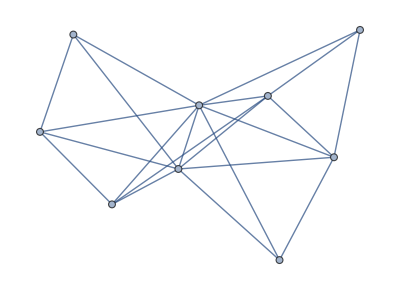
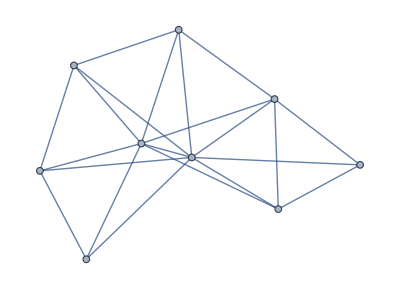
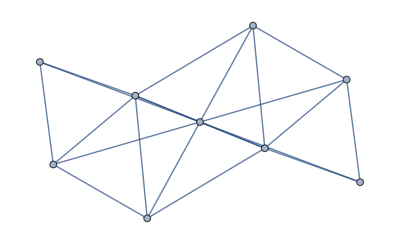
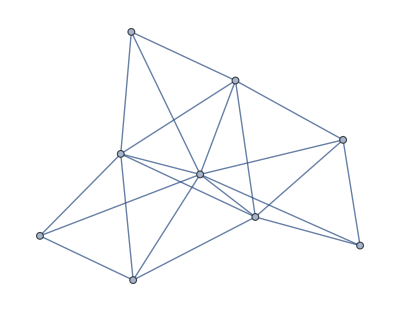
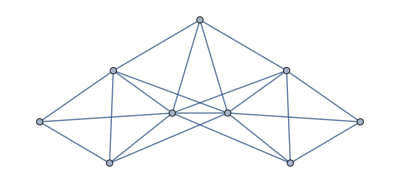
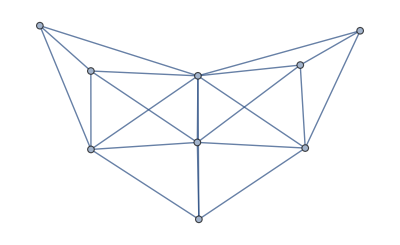
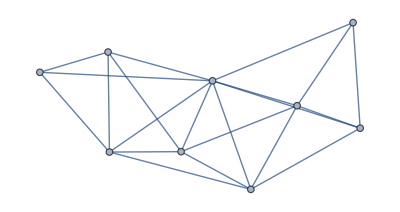
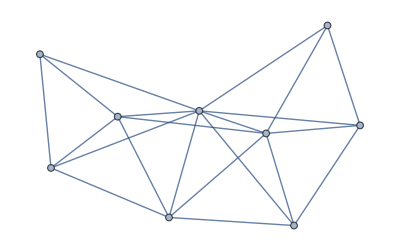

```mathematica
gr=Select[Map[Graph,ReadPlantri["D:\\cygwin64\\home\\alfre\\plantri9.txt"]],ChromaticPolynomial[#,4]==24&&PlanarGraphQ[#]&]
```

```mathematica
TableForm[Map[Map [Last,#]&,Map[FormulaLevels[FindFullFormula[#]]&,gr]],TableDepth->2]
```

1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1
1 | 31 | 90 | 65 | 15 | 1

```mathematica
TableForm[Map[GatherBy[FindFullFormula[#],SymbolLevel[#]&]&,gr],TableDepth->3]
```

{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x69x7x8}
{v1x2x3x4x5x68x7x9}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x27x3x4x5x6x8x9}
{v1x26x3x4x5x7x8x9}
{v1x25x3x4x6x7x8x9} | {v1x2x3x4x5x68x79}
{v1x2x3x4x59x68x7}
{v1x2x3x4x58x6x79}
{v1x2x3x4x58x69x7}
{v1x2x3x4x579x6x8}
{v1x2x3x4x57x69x8}
{v1x2x3x4x57x68x9}
{v1x2x3x49x5x68x7}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x39x4x5x68x7}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x38x4x5x6x79}
{v1x2x38x4x5x69x7}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x379x4x5x6x8}
{v1x2x37x4x5x69x8}
{v1x2x37x4x5x68x9}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x369x4x5x7x8}
{v1x2x368x4x5x7x9}
{v1x2x36x4x5x79x8}
{v1x2x36x4x59x7x8}
{v1x2x36x4x58x7x9}
{v1x2x36x4x57x8x9}
{v1x2x36x49x5x7x8}
{v1x2x359x4x6x7x8}
{v1x2x358x4x6x7x9}
{v1x2x357x4x6x8x9}
{v1x2x35x4x6x79x8}
{v1x2x35x4x69x7x8}
{v1x2x35x4x68x7x9}
{v1x2x35x49x6x7x8}
{v1x27x3x4x5x69x8}
{v1x27x3x4x5x68x9}
{v1x27x3x4x59x6x8}
{v1x27x3x4x58x6x9}
{v1x27x3x49x5x6x8}
{v1x27x39x4x5x6x8}
{v1x27x38x4x5x6x9}
{v1x27x36x4x5x8x9}
{v1x27x35x4x6x8x9}
{v1x26x3x4x5x79x8}
{v1x26x3x4x59x7x8}
{v1x26x3x4x58x7x9}
{v1x26x3x4x57x8x9}
{v1x26x3x49x5x7x8}
{v1x26x39x4x5x7x8}
{v1x26x38x4x5x7x9}
{v1x26x37x4x5x8x9}
{v1x26x35x4x7x8x9}
{v1x257x3x4x6x8x9}
{v1x25x3x4x6x79x8}
{v1x25x3x4x69x7x8}
{v1x25x3x4x68x7x9}
{v1x25x3x49x6x7x8}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x25x36x4x7x8x9} | {v1x2x3x4x579x68}
{v1x2x3x49x57x68}
{v1x2x39x4x57x68}
{v1x2x38x4x579x6}
{v1x2x38x4x57x69}
{v1x2x38x49x57x6}
{v1x2x379x4x5x68}
{v1x2x37x4x59x68}
{v1x2x379x4x58x6}
{v1x2x37x4x58x69}
{v1x2x37x49x5x68}
{v1x2x37x49x58x6}
{v1x2x368x4x5x79}
{v1x2x368x4x59x7}
{v1x2x369x4x58x7}
{v1x2x36x4x58x79}
{v1x2x36x4x579x8}
{v1x2x369x4x57x8}
{v1x2x368x4x57x9}
{v1x2x368x49x5x7}
{v1x2x36x49x58x7}
{v1x2x36x49x57x8}
{v1x2x3579x4x6x8}
{v1x2x358x4x6x79}
{v1x2x358x4x69x7}
{v1x2x357x4x69x8}
{v1x2x359x4x68x7}
{v1x2x357x4x68x9}
{v1x2x35x4x68x79}
{v1x2x358x49x6x7}
{v1x2x357x49x6x8}
{v1x2x35x49x68x7}
{v1x27x3x4x59x68}
{v1x27x3x4x58x69}
{v1x27x3x49x5x68}
{v1x27x3x49x58x6}
{v1x27x39x4x5x68}
{v1x27x39x4x58x6}
{v1x27x38x4x5x69}
{v1x27x38x4x59x6}
{v1x27x38x49x5x6}
{v1x27x369x4x5x8}
{v1x27x368x4x5x9}
{v1x27x36x4x59x8}
{v1x27x36x4x58x9}
{v1x27x36x49x5x8}
{v1x27x359x4x6x8}
{v1x27x358x4x6x9}
{v1x27x35x4x69x8}
{v1x27x35x4x68x9}
{v1x27x35x49x6x8}
{v1x26x3x4x58x79}
{v1x26x3x4x579x8}
{v1x26x3x49x58x7}
{v1x26x3x49x57x8}
{v1x26x39x4x58x7}
{v1x26x39x4x57x8}
{v1x26x38x4x5x79}
{v1x26x38x4x59x7}
{v1x26x38x4x57x9}
{v1x26x38x49x5x7}
{v1x26x379x4x5x8}
{v1x26x37x4x59x8}
{v1x26x37x4x58x9}
{v1x26x37x49x5x8}
{v1x26x359x4x7x8}
{v1x26x358x4x7x9}
{v1x26x357x4x8x9}
{v1x26x35x4x79x8}
{v1x26x35x49x7x8}
{v1x257x3x4x69x8}
{v1x257x3x4x68x9}
{v1x25x3x4x68x79}
{v1x257x3x49x6x8}
{v1x25x3x49x68x7}
{v1x257x39x4x6x8}
{v1x25x39x4x68x7}
{v1x257x38x4x6x9}
{v1x25x38x4x6x79}
{v1x25x38x4x69x7}
{v1x25x38x49x6x7}
{v1x25x379x4x6x8}
{v1x25x37x4x69x8}
{v1x25x37x4x68x9}
{v1x25x37x49x6x8}
{v1x25x369x4x7x8}
{v1x25x368x4x7x9}
{v1x257x36x4x8x9}
{v1x25x36x4x79x8}
{v1x25x36x49x7x8} | {v1x2x368x4x579}
{v1x2x368x49x57}
{v1x2x3579x4x68}
{v1x2x357x49x68}
{v1x27x368x4x59}
{v1x27x369x4x58}
{v1x27x368x49x5}
{v1x27x36x49x58}
{v1x27x358x4x69}
{v1x27x359x4x68}
{v1x27x358x49x6}
{v1x27x35x49x68}
{v1x26x38x4x579}
{v1x26x38x49x57}
{v1x26x379x4x58}
{v1x26x37x49x58}
{v1x26x3579x4x8}
{v1x26x358x4x79}
{v1x26x358x49x7}
{v1x26x357x49x8}
{v1x257x3x49x68}
{v1x257x39x4x68}
{v1x257x38x4x69}
{v1x257x38x49x6}
{v1x25x379x4x68}
{v1x25x37x49x68}
{v1x257x369x4x8}
{v1x257x368x4x9}
{v1x25x368x4x79}
{v1x25x368x49x7}
{v1x257x36x49x8} | {v1x257x368x49}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x69x7x8}
{v1x2x3x4x5x68x7x9}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x27x3x4x5x6x8x9}
{v1x26x3x4x5x7x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9} | {v1x2x3x4x5x68x79}
{v1x2x3x4x59x68x7}
{v1x2x3x4x58x6x79}
{v1x2x3x4x58x69x7}
{v1x2x3x4x579x6x8}
{v1x2x3x4x57x69x8}
{v1x2x3x4x57x68x9}
{v1x2x3x49x5x68x7}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x5x69x7}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x5x69x8}
{v1x2x3x47x5x68x9}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x3x469x5x7x8}
{v1x2x3x468x5x7x9}
{v1x2x3x46x5x79x8}
{v1x2x3x46x59x7x8}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x39x4x5x68x7}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x27x3x4x5x69x8}
{v1x27x3x4x5x68x9}
{v1x27x3x4x59x6x8}
{v1x27x3x4x58x6x9}
{v1x27x3x49x5x6x8}
{v1x27x3x48x5x6x9}
{v1x27x3x46x5x8x9}
{v1x27x39x4x5x6x8}
{v1x26x3x4x5x79x8}
{v1x26x3x4x59x7x8}
{v1x26x3x4x58x7x9}
{v1x26x3x4x57x8x9}
{v1x26x3x49x5x7x8}
{v1x26x3x48x5x7x9}
{v1x26x3x47x5x8x9}
{v1x26x39x4x5x7x8}
{v1x257x3x4x6x8x9}
{v1x25x3x4x6x79x8}
{v1x25x3x4x69x7x8}
{v1x25x3x4x68x7x9}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x39x4x6x7x8}
{v1x247x3x5x6x8x9}
{v1x24x3x5x6x79x8}
{v1x246x3x5x7x8x9}
{v1x24x3x5x69x7x8}
{v1x24x3x5x68x7x9}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x39x5x6x7x8} | {v1x2x3x4x579x68}
{v1x2x3x49x57x68}
{v1x2x3x48x579x6}
{v1x2x3x48x57x69}
{v1x2x3x479x5x68}
{v1x2x3x47x59x68}
{v1x2x3x479x58x6}
{v1x2x3x47x58x69}
{v1x2x3x468x5x79}
{v1x2x3x468x59x7}
{v1x2x3x469x58x7}
{v1x2x3x46x58x79}
{v1x2x3x46x579x8}
{v1x2x3x469x57x8}
{v1x2x3x468x57x9}
{v1x2x39x4x57x68}
{v1x2x39x48x57x6}
{v1x2x39x47x5x68}
{v1x2x39x47x58x6}
{v1x2x39x468x5x7}
{v1x2x39x46x58x7}
{v1x2x39x46x57x8}
{v1x27x3x4x59x68}
{v1x27x3x4x58x69}
{v1x27x3x49x5x68}
{v1x27x3x49x58x6}
{v1x27x3x48x5x69}
{v1x27x3x48x59x6}
{v1x27x3x469x5x8}
{v1x27x3x468x5x9}
{v1x27x3x46x59x8}
{v1x27x3x46x58x9}
{v1x27x39x4x5x68}
{v1x27x39x4x58x6}
{v1x27x39x48x5x6}
{v1x27x39x46x5x8}
{v1x26x3x4x58x79}
{v1x26x3x4x579x8}
{v1x26x3x49x58x7}
{v1x26x3x49x57x8}
{v1x26x3x48x5x79}
{v1x26x3x48x59x7}
{v1x26x3x48x57x9}
{v1x26x3x479x5x8}
{v1x26x3x47x59x8}
{v1x26x3x47x58x9}
{v1x26x39x4x58x7}
{v1x26x39x4x57x8}
{v1x26x39x48x5x7}
{v1x26x39x47x5x8}
{v1x257x3x4x69x8}
{v1x257x3x4x68x9}
{v1x25x3x4x68x79}
{v1x257x3x49x6x8}
{v1x25x3x49x68x7}
{v1x257x3x48x6x9}
{v1x25x3x48x6x79}
{v1x25x3x48x69x7}
{v1x25x3x479x6x8}
{v1x25x3x47x69x8}
{v1x25x3x47x68x9}
{v1x25x3x469x7x8}
{v1x25x3x468x7x9}
{v1x257x3x46x8x9}
{v1x25x3x46x79x8}
{v1x257x39x4x6x8}
{v1x25x39x4x68x7}
{v1x25x39x48x6x7}
{v1x25x39x47x6x8}
{v1x25x39x46x7x8}
{v1x246x3x5x79x8}
{v1x247x3x5x69x8}
{v1x247x3x5x68x9}
{v1x24x3x5x68x79}
{v1x247x3x59x6x8}
{v1x246x3x59x7x8}
{v1x24x3x59x68x7}
{v1x247x3x58x6x9}
{v1x24x3x58x6x79}
{v1x246x3x58x7x9}
{v1x24x3x58x69x7}
{v1x24x3x579x6x8}
{v1x246x3x57x8x9}
{v1x24x3x57x69x8}
{v1x24x3x57x68x9}
{v1x247x39x5x6x8}
{v1x246x39x5x7x8}
{v1x24x39x5x68x7}
{v1x24x39x58x6x7}
{v1x24x39x57x6x8} | {v1x2x3x468x579}
{v1x2x39x468x57}
{v1x27x3x468x59}
{v1x27x3x469x58}
{v1x27x39x468x5}
{v1x27x39x46x58}
{v1x26x3x48x579}
{v1x26x3x479x58}
{v1x26x39x48x57}
{v1x26x39x47x58}
{v1x257x3x49x68}
{v1x257x3x48x69}
{v1x25x3x479x68}
{v1x257x3x469x8}
{v1x257x3x468x9}
{v1x25x3x468x79}
{v1x257x39x4x68}
{v1x257x39x48x6}
{v1x25x39x47x68}
{v1x25x39x468x7}
{v1x257x39x46x8}
{v1x247x3x59x68}
{v1x246x3x58x79}
{v1x247x3x58x69}
{v1x246x3x579x8}
{v1x24x3x579x68}
{v1x247x39x5x68}
{v1x247x39x58x6}
{v1x246x39x58x7}
{v1x246x39x57x8}
{v1x24x39x57x68} | {v1x257x39x468}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x28x3x4x5x6x7x9}
{v1x27x3x4x5x6x8x9} | {v1x2x3x4x58x6x79}
{v1x2x3x4x579x6x8}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x3x46x5x79x8}
{v1x2x3x46x59x7x8}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x38x4x5x6x79}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x379x4x5x6x8}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x2x36x4x5x79x8}
{v1x2x36x4x59x7x8}
{v1x2x36x4x58x7x9}
{v1x2x36x4x57x8x9}
{v1x2x36x49x5x7x8}
{v1x2x36x48x5x7x9}
{v1x2x36x47x5x8x9}
{v1x2x359x4x6x7x8}
{v1x2x358x4x6x7x9}
{v1x2x357x4x6x8x9}
{v1x2x35x4x6x79x8}
{v1x2x35x49x6x7x8}
{v1x2x35x48x6x7x9}
{v1x2x35x47x6x8x9}
{v1x2x35x46x7x8x9}
{v1x28x3x4x5x6x79}
{v1x28x3x4x59x6x7}
{v1x28x3x4x57x6x9}
{v1x28x3x49x5x6x7}
{v1x28x3x47x5x6x9}
{v1x28x3x46x5x7x9}
{v1x28x39x4x5x6x7}
{v1x28x37x4x5x6x9}
{v1x28x36x4x5x7x9}
{v1x28x35x4x6x7x9}
{v1x27x3x4x59x6x8}
{v1x27x3x4x58x6x9}
{v1x27x3x49x5x6x8}
{v1x27x3x48x5x6x9}
{v1x27x3x46x5x8x9}
{v1x27x39x4x5x6x8}
{v1x27x38x4x5x6x9}
{v1x27x36x4x5x8x9}
{v1x27x35x4x6x8x9} | {v1x2x3x48x579x6}
{v1x2x3x479x58x6}
{v1x2x3x46x58x79}
{v1x2x3x46x579x8}
{v1x2x39x48x57x6}
{v1x2x39x47x58x6}
{v1x2x39x46x58x7}
{v1x2x39x46x57x8}
{v1x2x38x4x579x6}
{v1x2x38x49x57x6}
{v1x2x38x479x5x6}
{v1x2x38x47x59x6}
{v1x2x38x46x5x79}
{v1x2x38x46x59x7}
{v1x2x38x46x57x9}
{v1x2x379x4x58x6}
{v1x2x37x49x58x6}
{v1x2x379x48x5x6}
{v1x2x37x48x59x6}
{v1x2x379x46x5x8}
{v1x2x37x46x59x8}
{v1x2x37x46x58x9}
{v1x2x36x4x58x79}
{v1x2x36x4x579x8}
{v1x2x36x49x58x7}
{v1x2x36x49x57x8}
{v1x2x36x48x5x79}
{v1x2x36x48x59x7}
{v1x2x36x48x57x9}
{v1x2x36x479x5x8}
{v1x2x36x47x59x8}
{v1x2x36x47x58x9}
{v1x2x3579x4x6x8}
{v1x2x358x4x6x79}
{v1x2x358x49x6x7}
{v1x2x357x49x6x8}
{v1x2x359x48x6x7}
{v1x2x357x48x6x9}
{v1x2x35x48x6x79}
{v1x2x35x479x6x8}
{v1x2x359x47x6x8}
{v1x2x358x47x6x9}
{v1x2x359x46x7x8}
{v1x2x358x46x7x9}
{v1x2x357x46x8x9}
{v1x2x35x46x79x8}
{v1x28x3x4x579x6}
{v1x28x3x49x57x6}
{v1x28x3x479x5x6}
{v1x28x3x47x59x6}
{v1x28x3x46x5x79}
{v1x28x3x46x59x7}
{v1x28x3x46x57x9}
{v1x28x39x4x57x6}
{v1x28x39x47x5x6}
{v1x28x39x46x5x7}
{v1x28x379x4x5x6}
{v1x28x37x4x59x6}
{v1x28x37x49x5x6}
{v1x28x37x46x5x9}
{v1x28x36x4x5x79}
{v1x28x36x4x59x7}
{v1x28x36x4x57x9}
{v1x28x36x49x5x7}
{v1x28x36x47x5x9}
{v1x28x359x4x6x7}
{v1x28x357x4x6x9}
{v1x28x35x4x6x79}
{v1x28x35x49x6x7}
{v1x28x35x47x6x9}
{v1x28x35x46x7x9}
{v1x27x3x49x58x6}
{v1x27x3x48x59x6}
{v1x27x3x46x59x8}
{v1x27x3x46x58x9}
{v1x27x39x4x58x6}
{v1x27x39x48x5x6}
{v1x27x39x46x5x8}
{v1x27x38x4x59x6}
{v1x27x38x49x5x6}
{v1x27x38x46x5x9}
{v1x27x36x4x59x8}
{v1x27x36x4x58x9}
{v1x27x36x49x5x8}
{v1x27x36x48x5x9}
{v1x27x359x4x6x8}
{v1x27x358x4x6x9}
{v1x27x35x49x6x8}
{v1x27x35x48x6x9}
{v1x27x35x46x8x9} | {v1x2x38x46x579}
{v1x2x379x46x58}
{v1x2x36x48x579}
{v1x2x36x479x58}
{v1x2x3579x48x6}
{v1x2x358x479x6}
{v1x2x3579x46x8}
{v1x2x358x46x79}
{v1x28x3x46x579}
{v1x28x39x46x57}
{v1x28x379x46x5}
{v1x28x37x46x59}
{v1x28x36x4x579}
{v1x28x36x49x57}
{v1x28x36x479x5}
{v1x28x36x47x59}
{v1x28x3579x4x6}
{v1x28x357x49x6}
{v1x28x35x479x6}
{v1x28x359x47x6}
{v1x28x359x46x7}
{v1x28x357x46x9}
{v1x28x35x46x79}
{v1x27x39x46x58}
{v1x27x38x46x59}
{v1x27x36x49x58}
{v1x27x36x48x59}
{v1x27x358x49x6}
{v1x27x359x48x6}
{v1x27x359x46x8}
{v1x27x358x46x9} | {v1x28x3579x46}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x69x7x8}
{v1x2x3x4x5x68x7x9}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x48x5x6x7x9}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x28x3x4x5x6x7x9}
{v1x27x3x4x5x6x8x9}
{v1x26x3x4x5x7x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9} | {v1x2x3x4x59x68x7}
{v1x2x3x4x58x69x7}
{v1x2x3x4x57x69x8}
{v1x2x3x4x57x68x9}
{v1x2x3x48x5x69x7}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x38x4x5x69x7}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x37x4x5x69x8}
{v1x2x37x4x5x68x9}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x48x5x6x9}
{v1x2x368x4x5x7x9}
{v1x2x36x4x59x7x8}
{v1x2x36x4x58x7x9}
{v1x2x36x4x57x8x9}
{v1x2x36x48x5x7x9}
{v1x2x358x4x6x7x9}
{v1x2x357x4x6x8x9}
{v1x2x35x4x69x7x8}
{v1x2x35x4x68x7x9}
{v1x2x35x48x6x7x9}
{v1x28x3x4x5x69x7}
{v1x28x3x4x59x6x7}
{v1x28x3x4x57x6x9}
{v1x28x37x4x5x6x9}
{v1x28x36x4x5x7x9}
{v1x28x35x4x6x7x9}
{v1x27x3x4x5x69x8}
{v1x27x3x4x5x68x9}
{v1x27x3x4x59x6x8}
{v1x27x3x4x58x6x9}
{v1x27x3x48x5x6x9}
{v1x27x38x4x5x6x9}
{v1x27x36x4x5x8x9}
{v1x27x35x4x6x8x9}
{v1x268x3x4x5x7x9}
{v1x26x3x4x59x7x8}
{v1x26x3x4x58x7x9}
{v1x26x3x4x57x8x9}
{v1x26x3x48x5x7x9}
{v1x26x38x4x5x7x9}
{v1x26x37x4x5x8x9}
{v1x26x35x4x7x8x9}
{v1x258x3x4x6x7x9}
{v1x257x3x4x6x8x9}
{v1x25x3x4x69x7x8}
{v1x25x3x4x68x7x9}
{v1x25x3x48x6x7x9}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x25x36x4x7x8x9}
{v1x248x3x5x6x7x9}
{v1x24x3x5x69x7x8}
{v1x24x3x5x68x7x9}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x38x5x6x7x9}
{v1x24x37x5x6x8x9}
{v1x24x36x5x7x8x9}
{v1x24x35x6x7x8x9} | {v1x2x3x48x57x69}
{v1x2x38x4x57x69}
{v1x2x37x4x59x68}
{v1x2x37x4x58x69}
{v1x2x37x48x5x69}
{v1x2x37x48x59x6}
{v1x2x368x4x59x7}
{v1x2x368x4x57x9}
{v1x2x36x48x59x7}
{v1x2x36x48x57x9}
{v1x2x358x4x69x7}
{v1x2x357x4x69x8}
{v1x2x357x4x68x9}
{v1x2x357x48x6x9}
{v1x2x35x48x69x7}
{v1x28x3x4x57x69}
{v1x28x37x4x5x69}
{v1x28x37x4x59x6}
{v1x28x36x4x59x7}
{v1x28x36x4x57x9}
{v1x28x357x4x6x9}
{v1x28x35x4x69x7}
{v1x27x3x4x59x68}
{v1x27x3x4x58x69}
{v1x27x3x48x5x69}
{v1x27x3x48x59x6}
{v1x27x38x4x5x69}
{v1x27x38x4x59x6}
{v1x27x368x4x5x9}
{v1x27x36x4x59x8}
{v1x27x36x4x58x9}
{v1x27x36x48x5x9}
{v1x27x358x4x6x9}
{v1x27x35x4x69x8}
{v1x27x35x4x68x9}
{v1x27x35x48x6x9}
{v1x268x3x4x59x7}
{v1x268x3x4x57x9}
{v1x26x3x48x59x7}
{v1x26x3x48x57x9}
{v1x26x38x4x59x7}
{v1x26x38x4x57x9}
{v1x268x37x4x5x9}
{v1x26x37x4x59x8}
{v1x26x37x4x58x9}
{v1x26x37x48x5x9}
{v1x26x358x4x7x9}
{v1x268x35x4x7x9}
{v1x26x357x4x8x9}
{v1x26x35x48x7x9}
{v1x258x3x4x69x7}
{v1x257x3x4x69x8}
{v1x257x3x4x68x9}
{v1x257x3x48x6x9}
{v1x25x3x48x69x7}
{v1x257x38x4x6x9}
{v1x25x38x4x69x7}
{v1x258x37x4x6x9}
{v1x25x37x4x69x8}
{v1x25x37x4x68x9}
{v1x25x37x48x6x9}
{v1x25x368x4x7x9}
{v1x258x36x4x7x9}
{v1x257x36x4x8x9}
{v1x25x36x48x7x9}
{v1x248x3x5x69x7}
{v1x248x3x59x6x7}
{v1x24x3x59x68x7}
{v1x24x3x58x69x7}
{v1x248x3x57x6x9}
{v1x24x3x57x69x8}
{v1x24x3x57x68x9}
{v1x24x38x5x69x7}
{v1x24x38x59x6x7}
{v1x24x38x57x6x9}
{v1x248x37x5x6x9}
{v1x24x37x5x69x8}
{v1x24x37x5x68x9}
{v1x24x37x59x6x8}
{v1x24x37x58x6x9}
{v1x24x368x5x7x9}
{v1x248x36x5x7x9}
{v1x24x36x59x7x8}
{v1x24x36x58x7x9}
{v1x24x36x57x8x9}
{v1x24x358x6x7x9}
{v1x248x35x6x7x9}
{v1x24x357x6x8x9}
{v1x24x35x69x7x8}
{v1x24x35x68x7x9} | {v1x2x357x48x69}
{v1x28x357x4x69}
{v1x27x368x4x59}
{v1x27x36x48x59}
{v1x27x358x4x69}
{v1x27x35x48x69}
{v1x268x37x4x59}
{v1x26x37x48x59}
{v1x268x357x4x9}
{v1x26x357x48x9}
{v1x257x3x48x69}
{v1x257x38x4x69}
{v1x258x37x4x69}
{v1x25x37x48x69}
{v1x257x368x4x9}
{v1x257x36x48x9}
{v1x248x3x57x69}
{v1x24x38x57x69}
{v1x248x37x5x69}
{v1x248x37x59x6}
{v1x24x37x59x68}
{v1x24x37x58x69}
{v1x24x368x59x7}
{v1x248x36x59x7}
{v1x24x368x57x9}
{v1x248x36x57x9}
{v1x248x357x6x9}
{v1x24x358x69x7}
{v1x248x35x69x7}
{v1x24x357x69x8}
{v1x24x357x68x9} | {v1x248x357x69}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x7x89}
{v1x2x3x4x5x68x7x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x29x3x4x5x6x7x8}
{v1x27x3x4x5x6x8x9}
{v1x26x3x4x5x7x8x9}
{v19x2x3x4x5x6x7x8} | {v1x2x3x49x5x68x7}
{v1x2x3x489x5x6x7}
{v1x2x3x47x5x6x89}
{v1x2x3x47x5x68x9}
{v1x2x3x468x5x7x9}
{v1x2x3x46x5x7x89}
{v1x2x39x4x5x68x7}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x389x4x5x6x7}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x37x4x5x6x89}
{v1x2x37x4x5x68x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x2x368x4x5x7x9}
{v1x2x36x4x5x7x89}
{v1x2x36x49x5x7x8}
{v1x2x36x48x5x7x9}
{v1x2x36x47x5x8x9}
{v1x2x35x4x6x7x89}
{v1x2x35x4x68x7x9}
{v1x2x35x49x6x7x8}
{v1x2x35x48x6x7x9}
{v1x2x35x47x6x8x9}
{v1x2x35x46x7x8x9}
{v1x29x3x4x5x68x7}
{v1x29x3x48x5x6x7}
{v1x29x3x47x5x6x8}
{v1x29x3x46x5x7x8}
{v1x29x38x4x5x6x7}
{v1x29x37x4x5x6x8}
{v1x29x36x4x5x7x8}
{v1x29x35x4x6x7x8}
{v1x27x3x4x5x6x89}
{v1x27x3x4x5x68x9}
{v1x27x3x49x5x6x8}
{v1x27x3x48x5x6x9}
{v1x27x3x46x5x8x9}
{v1x27x39x4x5x6x8}
{v1x27x38x4x5x6x9}
{v1x27x36x4x5x8x9}
{v1x27x35x4x6x8x9}
{v1x26x3x4x5x7x89}
{v1x26x3x49x5x7x8}
{v1x26x3x48x5x7x9}
{v1x26x3x47x5x8x9}
{v1x26x39x4x5x7x8}
{v1x26x38x4x5x7x9}
{v1x26x37x4x5x8x9}
{v1x26x35x4x7x8x9}
{v19x2x3x4x5x68x7}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x38x4x5x6x7}
{v19x2x37x4x5x6x8}
{v19x2x36x4x5x7x8}
{v19x2x35x4x6x7x8}
{v19x27x3x4x5x6x8}
{v19x26x3x4x5x7x8} | {v1x2x39x47x5x68}
{v1x2x39x468x5x7}
{v1x2x389x47x5x6}
{v1x2x389x46x5x7}
{v1x2x37x49x5x68}
{v1x2x37x489x5x6}
{v1x2x37x468x5x9}
{v1x2x37x46x5x89}
{v1x2x368x49x5x7}
{v1x2x36x489x5x7}
{v1x2x368x47x5x9}
{v1x2x36x47x5x89}
{v1x2x35x49x68x7}
{v1x2x35x489x6x7}
{v1x2x35x47x6x89}
{v1x2x35x47x68x9}
{v1x2x35x468x7x9}
{v1x2x35x46x7x89}
{v1x29x3x47x5x68}
{v1x29x3x468x5x7}
{v1x29x38x47x5x6}
{v1x29x38x46x5x7}
{v1x29x37x4x5x68}
{v1x29x37x48x5x6}
{v1x29x37x46x5x8}
{v1x29x368x4x5x7}
{v1x29x36x48x5x7}
{v1x29x36x47x5x8}
{v1x29x35x4x68x7}
{v1x29x35x48x6x7}
{v1x29x35x47x6x8}
{v1x29x35x46x7x8}
{v1x27x3x49x5x68}
{v1x27x3x489x5x6}
{v1x27x3x468x5x9}
{v1x27x3x46x5x89}
{v1x27x39x4x5x68}
{v1x27x39x48x5x6}
{v1x27x39x46x5x8}
{v1x27x389x4x5x6}
{v1x27x38x49x5x6}
{v1x27x38x46x5x9}
{v1x27x368x4x5x9}
{v1x27x36x4x5x89}
{v1x27x36x49x5x8}
{v1x27x36x48x5x9}
{v1x27x35x4x6x89}
{v1x27x35x4x68x9}
{v1x27x35x49x6x8}
{v1x27x35x48x6x9}
{v1x27x35x46x8x9}
{v1x26x3x489x5x7}
{v1x26x3x47x5x89}
{v1x26x39x48x5x7}
{v1x26x39x47x5x8}
{v1x26x389x4x5x7}
{v1x26x38x49x5x7}
{v1x26x38x47x5x9}
{v1x26x37x4x5x89}
{v1x26x37x49x5x8}
{v1x26x37x48x5x9}
{v1x26x35x4x7x89}
{v1x26x35x49x7x8}
{v1x26x35x48x7x9}
{v1x26x35x47x8x9}
{v19x2x3x47x5x68}
{v19x2x3x468x5x7}
{v19x2x38x47x5x6}
{v19x2x38x46x5x7}
{v19x2x37x4x5x68}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x2x368x4x5x7}
{v19x2x36x48x5x7}
{v19x2x36x47x5x8}
{v19x2x35x4x68x7}
{v19x2x35x48x6x7}
{v19x2x35x47x6x8}
{v19x2x35x46x7x8}
{v19x27x3x4x5x68}
{v19x27x3x48x5x6}
{v19x27x3x46x5x8}
{v19x27x38x4x5x6}
{v19x27x36x4x5x8}
{v19x27x35x4x6x8}
{v19x26x3x48x5x7}
{v19x26x3x47x5x8}
{v19x26x38x4x5x7}
{v19x26x37x4x5x8}
{v19x26x35x4x7x8} | {v1x29x37x468x5}
{v1x29x368x47x5}
{v1x29x35x47x68}
{v1x29x35x468x7}
{v1x27x39x468x5}
{v1x27x389x46x5}
{v1x27x368x49x5}
{v1x27x36x489x5}
{v1x27x35x49x68}
{v1x27x35x489x6}
{v1x27x35x468x9}
{v1x27x35x46x89}
{v1x26x389x47x5}
{v1x26x37x489x5}
{v1x26x35x489x7}
{v1x26x35x47x89}
{v19x2x37x468x5}
{v19x2x368x47x5}
{v19x2x35x47x68}
{v19x2x35x468x7}
{v19x27x3x468x5}
{v19x27x38x46x5}
{v19x27x368x4x5}
{v19x27x36x48x5}
{v19x27x35x4x68}
{v19x27x35x48x6}
{v19x27x35x46x8}
{v19x26x38x47x5}
{v19x26x37x48x5}
{v19x26x35x48x7}
{v19x26x35x47x8} | {v19x27x35x468}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x69x7x8}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x28x3x4x5x6x7x9}
{v1x27x3x4x5x6x8x9}
{v1x26x3x4x5x7x8x9} | {v1x2x3x4x57x69x8}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x5x69x7}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x5x69x8}
{v1x2x3x469x5x7x8}
{v1x2x3x46x5x79x8}
{v1x2x3x46x57x8x9}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x38x4x5x6x79}
{v1x2x38x4x5x69x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x379x4x5x6x8}
{v1x2x37x4x5x69x8}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x2x369x4x5x7x8}
{v1x2x36x4x5x79x8}
{v1x2x36x4x57x8x9}
{v1x2x36x49x5x7x8}
{v1x2x36x48x5x7x9}
{v1x2x36x47x5x8x9}
{v1x2x357x4x6x8x9}
{v1x2x35x4x6x79x8}
{v1x2x35x4x69x7x8}
{v1x2x35x49x6x7x8}
{v1x2x35x48x6x7x9}
{v1x2x35x47x6x8x9}
{v1x2x35x46x7x8x9}
{v1x28x3x4x5x6x79}
{v1x28x3x4x5x69x7}
{v1x28x3x4x57x6x9}
{v1x28x3x49x5x6x7}
{v1x28x3x47x5x6x9}
{v1x28x3x46x5x7x9}
{v1x28x39x4x5x6x7}
{v1x28x37x4x5x6x9}
{v1x28x36x4x5x7x9}
{v1x28x35x4x6x7x9}
{v1x27x3x4x5x69x8}
{v1x27x3x49x5x6x8}
{v1x27x3x48x5x6x9}
{v1x27x3x46x5x8x9}
{v1x27x39x4x5x6x8}
{v1x27x38x4x5x6x9}
{v1x27x36x4x5x8x9}
{v1x27x35x4x6x8x9}
{v1x26x3x4x5x79x8}
{v1x26x3x4x57x8x9}
{v1x26x3x49x5x7x8}
{v1x26x3x48x5x7x9}
{v1x26x3x47x5x8x9}
{v1x26x39x4x5x7x8}
{v1x26x38x4x5x7x9}
{v1x26x37x4x5x8x9}
{v1x26x35x4x7x8x9} | {v1x2x3x48x57x69}
{v1x2x3x469x57x8}
{v1x2x39x48x57x6}
{v1x2x39x46x57x8}
{v1x2x38x4x57x69}
{v1x2x38x49x57x6}
{v1x2x38x479x5x6}
{v1x2x38x47x5x69}
{v1x2x38x469x5x7}
{v1x2x38x46x5x79}
{v1x2x38x46x57x9}
{v1x2x379x48x5x6}
{v1x2x37x48x5x69}
{v1x2x37x469x5x8}
{v1x2x379x46x5x8}
{v1x2x369x4x57x8}
{v1x2x36x49x57x8}
{v1x2x369x48x5x7}
{v1x2x36x48x5x79}
{v1x2x36x48x57x9}
{v1x2x36x479x5x8}
{v1x2x369x47x5x8}
{v1x2x357x4x69x8}
{v1x2x357x49x6x8}
{v1x2x357x48x6x9}
{v1x2x35x48x6x79}
{v1x2x35x48x69x7}
{v1x2x35x479x6x8}
{v1x2x35x47x69x8}
{v1x2x35x469x7x8}
{v1x2x357x46x8x9}
{v1x2x35x46x79x8}
{v1x28x3x4x57x69}
{v1x28x3x49x57x6}
{v1x28x3x479x5x6}
{v1x28x3x47x5x69}
{v1x28x3x469x5x7}
{v1x28x3x46x5x79}
{v1x28x3x46x57x9}
{v1x28x39x4x57x6}
{v1x28x39x47x5x6}
{v1x28x39x46x5x7}
{v1x28x379x4x5x6}
{v1x28x37x4x5x69}
{v1x28x37x49x5x6}
{v1x28x37x46x5x9}
{v1x28x369x4x5x7}
{v1x28x36x4x5x79}
{v1x28x36x4x57x9}
{v1x28x36x49x5x7}
{v1x28x36x47x5x9}
{v1x28x357x4x6x9}
{v1x28x35x4x6x79}
{v1x28x35x4x69x7}
{v1x28x35x49x6x7}
{v1x28x35x47x6x9}
{v1x28x35x46x7x9}
{v1x27x3x48x5x69}
{v1x27x3x469x5x8}
{v1x27x39x48x5x6}
{v1x27x39x46x5x8}
{v1x27x38x4x5x69}
{v1x27x38x49x5x6}
{v1x27x38x46x5x9}
{v1x27x369x4x5x8}
{v1x27x36x49x5x8}
{v1x27x36x48x5x9}
{v1x27x35x4x69x8}
{v1x27x35x49x6x8}
{v1x27x35x48x6x9}
{v1x27x35x46x8x9}
{v1x26x3x49x57x8}
{v1x26x3x48x5x79}
{v1x26x3x48x57x9}
{v1x26x3x479x5x8}
{v1x26x39x4x57x8}
{v1x26x39x48x5x7}
{v1x26x39x47x5x8}
{v1x26x38x4x5x79}
{v1x26x38x4x57x9}
{v1x26x38x49x5x7}
{v1x26x38x47x5x9}
{v1x26x379x4x5x8}
{v1x26x37x49x5x8}
{v1x26x37x48x5x9}
{v1x26x357x4x8x9}
{v1x26x35x4x79x8}
{v1x26x35x49x7x8}
{v1x26x35x48x7x9}
{v1x26x35x47x8x9} | {v1x2x38x469x57}
{v1x2x369x48x57}
{v1x2x357x48x69}
{v1x2x357x469x8}
{v1x28x3x469x57}
{v1x28x39x46x57}
{v1x28x37x469x5}
{v1x28x379x46x5}
{v1x28x369x4x57}
{v1x28x36x49x57}
{v1x28x36x479x5}
{v1x28x369x47x5}
{v1x28x357x4x69}
{v1x28x357x49x6}
{v1x28x35x479x6}
{v1x28x35x47x69}
{v1x28x35x469x7}
{v1x28x357x46x9}
{v1x28x35x46x79}
{v1x27x38x469x5}
{v1x27x369x48x5}
{v1x27x35x48x69}
{v1x27x35x469x8}
{v1x26x39x48x57}
{v1x26x38x49x57}
{v1x26x38x479x5}
{v1x26x379x48x5}
{v1x26x357x49x8}
{v1x26x357x48x9}
{v1x26x35x48x79}
{v1x26x35x479x8} | {v1x28x357x469}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x28x3x4x5x6x7x9}
{v1x27x3x4x5x6x8x9}
{v1x26x3x4x5x7x8x9} | {v1x2x3x4x58x6x79}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x58x6x9}
{v1x2x3x46x5x79x8}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x38x4x5x6x79}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x379x4x5x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x2x36x4x5x79x8}
{v1x2x36x4x58x7x9}
{v1x2x36x4x57x8x9}
{v1x2x36x49x5x7x8}
{v1x2x36x48x5x7x9}
{v1x2x36x47x5x8x9}
{v1x2x358x4x6x7x9}
{v1x2x357x4x6x8x9}
{v1x2x35x4x6x79x8}
{v1x2x35x49x6x7x8}
{v1x2x35x48x6x7x9}
{v1x2x35x47x6x8x9}
{v1x2x35x46x7x8x9}
{v1x28x3x4x5x6x79}
{v1x28x3x4x57x6x9}
{v1x28x3x49x5x6x7}
{v1x28x3x47x5x6x9}
{v1x28x3x46x5x7x9}
{v1x28x39x4x5x6x7}
{v1x28x37x4x5x6x9}
{v1x28x36x4x5x7x9}
{v1x28x35x4x6x7x9}
{v1x27x3x4x58x6x9}
{v1x27x3x49x5x6x8}
{v1x27x3x48x5x6x9}
{v1x27x3x46x5x8x9}
{v1x27x39x4x5x6x8}
{v1x27x38x4x5x6x9}
{v1x27x36x4x5x8x9}
{v1x27x35x4x6x8x9}
{v1x26x3x4x5x79x8}
{v1x26x3x4x58x7x9}
{v1x26x3x4x57x8x9}
{v1x26x3x49x5x7x8}
{v1x26x3x48x5x7x9}
{v1x26x3x47x5x8x9}
{v1x26x39x4x5x7x8}
{v1x26x38x4x5x7x9}
{v1x26x37x4x5x8x9}
{v1x26x35x4x7x8x9} | {v1x2x3x479x58x6}
{v1x2x3x46x58x79}
{v1x2x39x48x57x6}
{v1x2x39x47x58x6}
{v1x2x39x46x58x7}
{v1x2x39x46x57x8}
{v1x2x38x49x57x6}
{v1x2x38x479x5x6}
{v1x2x38x46x5x79}
{v1x2x38x46x57x9}
{v1x2x379x4x58x6}
{v1x2x37x49x58x6}
{v1x2x379x48x5x6}
{v1x2x379x46x5x8}
{v1x2x37x46x58x9}
{v1x2x36x4x58x79}
{v1x2x36x49x58x7}
{v1x2x36x49x57x8}
{v1x2x36x48x5x79}
{v1x2x36x48x57x9}
{v1x2x36x479x5x8}
{v1x2x36x47x58x9}
{v1x2x358x4x6x79}
{v1x2x358x49x6x7}
{v1x2x357x49x6x8}
{v1x2x357x48x6x9}
{v1x2x35x48x6x79}
{v1x2x35x479x6x8}
{v1x2x358x47x6x9}
{v1x2x358x46x7x9}
{v1x2x357x46x8x9}
{v1x2x35x46x79x8}
{v1x28x3x49x57x6}
{v1x28x3x479x5x6}
{v1x28x3x46x5x79}
{v1x28x3x46x57x9}
{v1x28x39x4x57x6}
{v1x28x39x47x5x6}
{v1x28x39x46x5x7}
{v1x28x379x4x5x6}
{v1x28x37x49x5x6}
{v1x28x37x46x5x9}
{v1x28x36x4x5x79}
{v1x28x36x4x57x9}
{v1x28x36x49x5x7}
{v1x28x36x47x5x9}
{v1x28x357x4x6x9}
{v1x28x35x4x6x79}
{v1x28x35x49x6x7}
{v1x28x35x47x6x9}
{v1x28x35x46x7x9}
{v1x27x3x49x58x6}
{v1x27x3x46x58x9}
{v1x27x39x4x58x6}
{v1x27x39x48x5x6}
{v1x27x39x46x5x8}
{v1x27x38x49x5x6}
{v1x27x38x46x5x9}
{v1x27x36x4x58x9}
{v1x27x36x49x5x8}
{v1x27x36x48x5x9}
{v1x27x358x4x6x9}
{v1x27x35x49x6x8}
{v1x27x35x48x6x9}
{v1x27x35x46x8x9}
{v1x26x3x4x58x79}
{v1x26x3x49x58x7}
{v1x26x3x49x57x8}
{v1x26x3x48x5x79}
{v1x26x3x48x57x9}
{v1x26x3x479x5x8}
{v1x26x3x47x58x9}
{v1x26x39x4x58x7}
{v1x26x39x4x57x8}
{v1x26x39x48x5x7}
{v1x26x39x47x5x8}
{v1x26x38x4x5x79}
{v1x26x38x4x57x9}
{v1x26x38x49x5x7}
{v1x26x38x47x5x9}
{v1x26x379x4x5x8}
{v1x26x37x4x58x9}
{v1x26x37x49x5x8}
{v1x26x37x48x5x9}
{v1x26x358x4x7x9}
{v1x26x357x4x8x9}
{v1x26x35x4x79x8}
{v1x26x35x49x7x8}
{v1x26x35x48x7x9}
{v1x26x35x47x8x9} | {v1x2x379x46x58}
{v1x2x36x479x58}
{v1x2x358x479x6}
{v1x2x358x46x79}
{v1x28x39x46x57}
{v1x28x379x46x5}
{v1x28x36x49x57}
{v1x28x36x479x5}
{v1x28x357x49x6}
{v1x28x35x479x6}
{v1x28x357x46x9}
{v1x28x35x46x79}
{v1x27x39x46x58}
{v1x27x36x49x58}
{v1x27x358x49x6}
{v1x27x358x46x9}
{v1x26x3x479x58}
{v1x26x39x48x57}
{v1x26x39x47x58}
{v1x26x38x49x57}
{v1x26x38x479x5}
{v1x26x379x4x58}
{v1x26x37x49x58}
{v1x26x379x48x5}
{v1x26x358x4x79}
{v1x26x358x49x7}
{v1x26x357x49x8}
{v1x26x357x48x9}
{v1x26x35x48x79}
{v1x26x35x479x8}
{v1x26x358x47x9} | {v1x26x358x479}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x69x7x8}
{v1x2x3x4x5x68x7x9}
{v1x2x3x4x59x6x7x8}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x28x3x4x5x6x7x9}
{v1x27x3x4x5x6x8x9}
{v1x26x3x4x5x7x8x9}
{v1x25x3x4x6x7x8x9} | {v1x2x3x4x5x68x79}
{v1x2x3x4x59x68x7}
{v1x2x3x47x5x69x8}
{v1x2x3x47x5x68x9}
{v1x2x3x47x59x6x8}
{v1x2x3x46x5x79x8}
{v1x2x3x46x59x7x8}
{v1x2x39x4x5x68x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x38x4x5x6x79}
{v1x2x38x4x5x69x7}
{v1x2x38x4x59x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x379x4x5x6x8}
{v1x2x37x4x5x69x8}
{v1x2x37x4x5x68x9}
{v1x2x37x4x59x6x8}
{v1x2x37x46x5x8x9}
{v1x2x369x4x5x7x8}
{v1x2x368x4x5x7x9}
{v1x2x36x4x5x79x8}
{v1x2x36x4x59x7x8}
{v1x2x36x47x5x8x9}
{v1x2x359x4x6x7x8}
{v1x2x35x4x6x79x8}
{v1x2x35x4x69x7x8}
{v1x2x35x4x68x7x9}
{v1x2x35x47x6x8x9}
{v1x2x35x46x7x8x9}
{v1x28x3x4x5x6x79}
{v1x28x3x4x5x69x7}
{v1x28x3x4x59x6x7}
{v1x28x3x47x5x6x9}
{v1x28x3x46x5x7x9}
{v1x28x39x4x5x6x7}
{v1x28x37x4x5x6x9}
{v1x28x36x4x5x7x9}
{v1x28x35x4x6x7x9}
{v1x27x3x4x5x69x8}
{v1x27x3x4x5x68x9}
{v1x27x3x4x59x6x8}
{v1x27x3x46x5x8x9}
{v1x27x39x4x5x6x8}
{v1x27x38x4x5x6x9}
{v1x27x36x4x5x8x9}
{v1x27x35x4x6x8x9}
{v1x268x3x4x5x7x9}
{v1x26x3x4x5x79x8}
{v1x26x3x4x59x7x8}
{v1x26x3x47x5x8x9}
{v1x26x39x4x5x7x8}
{v1x26x38x4x5x7x9}
{v1x26x37x4x5x8x9}
{v1x26x35x4x7x8x9}
{v1x25x3x4x6x79x8}
{v1x25x3x4x69x7x8}
{v1x25x3x4x68x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x25x36x4x7x8x9} | {v1x2x3x47x59x68}
{v1x2x39x47x5x68}
{v1x2x38x47x5x69}
{v1x2x38x47x59x6}
{v1x2x38x46x5x79}
{v1x2x38x46x59x7}
{v1x2x379x4x5x68}
{v1x2x37x4x59x68}
{v1x2x379x46x5x8}
{v1x2x37x46x59x8}
{v1x2x368x4x5x79}
{v1x2x368x4x59x7}
{v1x2x369x47x5x8}
{v1x2x368x47x5x9}
{v1x2x36x47x59x8}
{v1x2x359x4x68x7}
{v1x2x35x4x68x79}
{v1x2x359x47x6x8}
{v1x2x35x47x69x8}
{v1x2x35x47x68x9}
{v1x2x359x46x7x8}
{v1x2x35x46x79x8}
{v1x28x3x47x5x69}
{v1x28x3x47x59x6}
{v1x28x3x46x5x79}
{v1x28x3x46x59x7}
{v1x28x39x47x5x6}
{v1x28x39x46x5x7}
{v1x28x379x4x5x6}
{v1x28x37x4x5x69}
{v1x28x37x4x59x6}
{v1x28x37x46x5x9}
{v1x28x369x4x5x7}
{v1x28x36x4x5x79}
{v1x28x36x4x59x7}
{v1x28x36x47x5x9}
{v1x28x359x4x6x7}
{v1x28x35x4x6x79}
{v1x28x35x4x69x7}
{v1x28x35x47x6x9}
{v1x28x35x46x7x9}
{v1x27x3x4x59x68}
{v1x27x3x46x59x8}
{v1x27x39x4x5x68}
{v1x27x39x46x5x8}
{v1x27x38x4x5x69}
{v1x27x38x4x59x6}
{v1x27x38x46x5x9}
{v1x27x369x4x5x8}
{v1x27x368x4x5x9}
{v1x27x36x4x59x8}
{v1x27x359x4x6x8}
{v1x27x35x4x69x8}
{v1x27x35x4x68x9}
{v1x27x35x46x8x9}
{v1x268x3x4x5x79}
{v1x268x3x4x59x7}
{v1x268x3x47x5x9}
{v1x26x3x47x59x8}
{v1x268x39x4x5x7}
{v1x26x39x47x5x8}
{v1x26x38x4x5x79}
{v1x26x38x4x59x7}
{v1x26x38x47x5x9}
{v1x26x379x4x5x8}
{v1x268x37x4x5x9}
{v1x26x37x4x59x8}
{v1x26x359x4x7x8}
{v1x268x35x4x7x9}
{v1x26x35x4x79x8}
{v1x26x35x47x8x9}
{v1x25x3x4x68x79}
{v1x25x3x47x69x8}
{v1x25x3x47x68x9}
{v1x25x3x46x79x8}
{v1x25x39x4x68x7}
{v1x25x39x47x6x8}
{v1x25x39x46x7x8}
{v1x25x38x4x6x79}
{v1x25x38x4x69x7}
{v1x25x38x47x6x9}
{v1x25x38x46x7x9}
{v1x25x379x4x6x8}
{v1x25x37x4x69x8}
{v1x25x37x4x68x9}
{v1x25x37x46x8x9}
{v1x25x369x4x7x8}
{v1x25x368x4x7x9}
{v1x25x36x4x79x8}
{v1x25x36x47x8x9} | {v1x2x368x47x59}
{v1x2x359x47x68}
{v1x28x379x46x5}
{v1x28x37x46x59}
{v1x28x369x47x5}
{v1x28x36x47x59}
{v1x28x359x47x6}
{v1x28x35x47x69}
{v1x28x359x46x7}
{v1x28x35x46x79}
{v1x27x38x46x59}
{v1x27x368x4x59}
{v1x27x359x4x68}
{v1x27x359x46x8}
{v1x268x3x47x59}
{v1x268x39x47x5}
{v1x26x38x47x59}
{v1x268x379x4x5}
{v1x268x37x4x59}
{v1x268x359x4x7}
{v1x268x35x4x79}
{v1x26x359x47x8}
{v1x268x35x47x9}
{v1x25x39x47x68}
{v1x25x38x47x69}
{v1x25x38x46x79}
{v1x25x379x4x68}
{v1x25x379x46x8}
{v1x25x368x4x79}
{v1x25x369x47x8}
{v1x25x368x47x9} | {v1x268x359x47}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x69x7x8}
{v1x2x3x4x5x68x7x9}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x26x3x4x5x7x8x9}
{v1x25x3x4x6x7x8x9} | {v1x2x3x4x5x68x79}
{v1x2x3x4x59x68x7}
{v1x2x3x4x58x6x79}
{v1x2x3x4x58x69x7}
{v1x2x3x4x579x6x8}
{v1x2x3x4x57x69x8}
{v1x2x3x4x57x68x9}
{v1x2x3x49x5x68x7}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x5x69x7}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x39x4x5x68x7}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x38x4x5x6x79}
{v1x2x38x4x5x69x7}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x379x4x5x6x8}
{v1x2x37x4x5x69x8}
{v1x2x37x4x5x68x9}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x369x4x5x7x8}
{v1x2x368x4x5x7x9}
{v1x2x36x4x5x79x8}
{v1x2x36x4x59x7x8}
{v1x2x36x4x58x7x9}
{v1x2x36x4x57x8x9}
{v1x2x36x49x5x7x8}
{v1x2x36x48x5x7x9}
{v1x2x359x4x6x7x8}
{v1x2x358x4x6x7x9}
{v1x2x357x4x6x8x9}
{v1x2x35x4x6x79x8}
{v1x2x35x4x69x7x8}
{v1x2x35x4x68x7x9}
{v1x2x35x49x6x7x8}
{v1x2x35x48x6x7x9}
{v1x26x3x4x5x79x8}
{v1x26x3x4x59x7x8}
{v1x26x3x4x58x7x9}
{v1x26x3x4x57x8x9}
{v1x26x3x49x5x7x8}
{v1x26x3x48x5x7x9}
{v1x26x39x4x5x7x8}
{v1x26x38x4x5x7x9}
{v1x26x37x4x5x8x9}
{v1x26x35x4x7x8x9}
{v1x25x3x4x6x79x8}
{v1x25x3x4x69x7x8}
{v1x25x3x4x68x7x9}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x25x36x4x7x8x9} | {v1x2x3x4x579x68}
{v1x2x3x49x57x68}
{v1x2x3x48x579x6}
{v1x2x3x48x57x69}
{v1x2x39x4x57x68}
{v1x2x39x48x57x6}
{v1x2x38x4x579x6}
{v1x2x38x4x57x69}
{v1x2x38x49x57x6}
{v1x2x379x4x5x68}
{v1x2x37x4x59x68}
{v1x2x379x4x58x6}
{v1x2x37x4x58x69}
{v1x2x37x49x5x68}
{v1x2x37x49x58x6}
{v1x2x379x48x5x6}
{v1x2x37x48x5x69}
{v1x2x37x48x59x6}
{v1x2x368x4x5x79}
{v1x2x368x4x59x7}
{v1x2x369x4x58x7}
{v1x2x36x4x58x79}
{v1x2x36x4x579x8}
{v1x2x369x4x57x8}
{v1x2x368x4x57x9}
{v1x2x368x49x5x7}
{v1x2x36x49x58x7}
{v1x2x36x49x57x8}
{v1x2x369x48x5x7}
{v1x2x36x48x5x79}
{v1x2x36x48x59x7}
{v1x2x36x48x57x9}
{v1x2x3579x4x6x8}
{v1x2x358x4x6x79}
{v1x2x358x4x69x7}
{v1x2x357x4x69x8}
{v1x2x359x4x68x7}
{v1x2x357x4x68x9}
{v1x2x35x4x68x79}
{v1x2x358x49x6x7}
{v1x2x357x49x6x8}
{v1x2x35x49x68x7}
{v1x2x359x48x6x7}
{v1x2x357x48x6x9}
{v1x2x35x48x6x79}
{v1x2x35x48x69x7}
{v1x26x3x4x58x79}
{v1x26x3x4x579x8}
{v1x26x3x49x58x7}
{v1x26x3x49x57x8}
{v1x26x3x48x5x79}
{v1x26x3x48x59x7}
{v1x26x3x48x57x9}
{v1x26x39x4x58x7}
{v1x26x39x4x57x8}
{v1x26x39x48x5x7}
{v1x26x38x4x5x79}
{v1x26x38x4x59x7}
{v1x26x38x4x57x9}
{v1x26x38x49x5x7}
{v1x26x379x4x5x8}
{v1x26x37x4x59x8}
{v1x26x37x4x58x9}
{v1x26x37x49x5x8}
{v1x26x37x48x5x9}
{v1x26x359x4x7x8}
{v1x26x358x4x7x9}
{v1x26x357x4x8x9}
{v1x26x35x4x79x8}
{v1x26x35x49x7x8}
{v1x26x35x48x7x9}
{v1x25x3x4x68x79}
{v1x25x3x49x68x7}
{v1x25x3x48x6x79}
{v1x25x3x48x69x7}
{v1x25x39x4x68x7}
{v1x25x39x48x6x7}
{v1x25x38x4x6x79}
{v1x25x38x4x69x7}
{v1x25x38x49x6x7}
{v1x25x379x4x6x8}
{v1x25x37x4x69x8}
{v1x25x37x4x68x9}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x369x4x7x8}
{v1x25x368x4x7x9}
{v1x25x36x4x79x8}
{v1x25x36x49x7x8}
{v1x25x36x48x7x9} | {v1x2x368x4x579}
{v1x2x368x49x57}
{v1x2x36x48x579}
{v1x2x369x48x57}
{v1x2x3579x4x68}
{v1x2x357x49x68}
{v1x2x3579x48x6}
{v1x2x357x48x69}
{v1x26x3x48x579}
{v1x26x39x48x57}
{v1x26x38x4x579}
{v1x26x38x49x57}
{v1x26x379x4x58}
{v1x26x37x49x58}
{v1x26x379x48x5}
{v1x26x37x48x59}
{v1x26x3579x4x8}
{v1x26x358x4x79}
{v1x26x358x49x7}
{v1x26x357x49x8}
{v1x26x359x48x7}
{v1x26x357x48x9}
{v1x26x35x48x79}
{v1x25x379x4x68}
{v1x25x37x49x68}
{v1x25x379x48x6}
{v1x25x37x48x69}
{v1x25x368x4x79}
{v1x25x368x49x7}
{v1x25x369x48x7}
{v1x25x36x48x79} | {v1x26x3579x48}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x69x7x8}
{v1x2x3x4x5x68x7x9}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x36x4x5x7x8x9}
{v1x26x3x4x5x7x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9} | {v1x2x3x4x5x68x79}
{v1x2x3x4x59x68x7}
{v1x2x3x4x58x6x79}
{v1x2x3x4x58x69x7}
{v1x2x3x49x5x68x7}
{v1x2x3x49x58x6x7}
{v1x2x3x48x5x6x79}
{v1x2x3x48x5x69x7}
{v1x2x3x48x59x6x7}
{v1x2x3x479x5x6x8}
{v1x2x3x47x5x69x8}
{v1x2x3x47x5x68x9}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x3x469x5x7x8}
{v1x2x3x468x5x7x9}
{v1x2x3x46x5x79x8}
{v1x2x3x46x59x7x8}
{v1x2x3x46x58x7x9}
{v1x2x39x4x5x68x7}
{v1x2x39x4x58x6x7}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x38x4x5x6x79}
{v1x2x38x4x5x69x7}
{v1x2x38x4x59x6x7}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x369x4x5x7x8}
{v1x2x368x4x5x7x9}
{v1x2x36x4x5x79x8}
{v1x2x36x4x59x7x8}
{v1x2x36x4x58x7x9}
{v1x2x36x49x5x7x8}
{v1x2x36x48x5x7x9}
{v1x2x36x47x5x8x9}
{v1x26x3x4x5x79x8}
{v1x26x3x4x59x7x8}
{v1x26x3x4x58x7x9}
{v1x26x3x49x5x7x8}
{v1x26x3x48x5x7x9}
{v1x26x3x47x5x8x9}
{v1x26x39x4x5x7x8}
{v1x26x38x4x5x7x9}
{v1x25x3x4x6x79x8}
{v1x25x3x4x69x7x8}
{v1x25x3x4x68x7x9}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x36x4x7x8x9}
{v1x24x3x5x6x79x8}
{v1x246x3x5x7x8x9}
{v1x24x3x5x69x7x8}
{v1x24x3x5x68x7x9}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x39x5x6x7x8}
{v1x24x38x5x6x7x9}
{v1x24x36x5x7x8x9} | {v1x2x3x479x5x68}
{v1x2x3x47x59x68}
{v1x2x3x479x58x6}
{v1x2x3x47x58x69}
{v1x2x3x468x5x79}
{v1x2x3x468x59x7}
{v1x2x3x469x58x7}
{v1x2x3x46x58x79}
{v1x2x39x47x5x68}
{v1x2x39x47x58x6}
{v1x2x39x468x5x7}
{v1x2x39x46x58x7}
{v1x2x38x479x5x6}
{v1x2x38x47x5x69}
{v1x2x38x47x59x6}
{v1x2x38x469x5x7}
{v1x2x38x46x5x79}
{v1x2x38x46x59x7}
{v1x2x368x4x5x79}
{v1x2x368x4x59x7}
{v1x2x369x4x58x7}
{v1x2x36x4x58x79}
{v1x2x368x49x5x7}
{v1x2x36x49x58x7}
{v1x2x369x48x5x7}
{v1x2x36x48x5x79}
{v1x2x36x48x59x7}
{v1x2x36x479x5x8}
{v1x2x369x47x5x8}
{v1x2x368x47x5x9}
{v1x2x36x47x59x8}
{v1x2x36x47x58x9}
{v1x26x3x4x58x79}
{v1x26x3x49x58x7}
{v1x26x3x48x5x79}
{v1x26x3x48x59x7}
{v1x26x3x479x5x8}
{v1x26x3x47x59x8}
{v1x26x3x47x58x9}
{v1x26x39x4x58x7}
{v1x26x39x48x5x7}
{v1x26x39x47x5x8}
{v1x26x38x4x5x79}
{v1x26x38x4x59x7}
{v1x26x38x49x5x7}
{v1x26x38x47x5x9}
{v1x25x3x4x68x79}
{v1x25x3x49x68x7}
{v1x25x3x48x6x79}
{v1x25x3x48x69x7}
{v1x25x3x479x6x8}
{v1x25x3x47x69x8}
{v1x25x3x47x68x9}
{v1x25x3x469x7x8}
{v1x25x3x468x7x9}
{v1x25x3x46x79x8}
{v1x25x39x4x68x7}
{v1x25x39x48x6x7}
{v1x25x39x47x6x8}
{v1x25x39x46x7x8}
{v1x25x38x4x6x79}
{v1x25x38x4x69x7}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x38x46x7x9}
{v1x25x369x4x7x8}
{v1x25x368x4x7x9}
{v1x25x36x4x79x8}
{v1x25x36x49x7x8}
{v1x25x36x48x7x9}
{v1x25x36x47x8x9}
{v1x246x3x5x79x8}
{v1x24x3x5x68x79}
{v1x246x3x59x7x8}
{v1x24x3x59x68x7}
{v1x24x3x58x6x79}
{v1x246x3x58x7x9}
{v1x24x3x58x69x7}
{v1x246x39x5x7x8}
{v1x24x39x5x68x7}
{v1x24x39x58x6x7}
{v1x24x38x5x6x79}
{v1x246x38x5x7x9}
{v1x24x38x5x69x7}
{v1x24x38x59x6x7}
{v1x24x369x5x7x8}
{v1x24x368x5x7x9}
{v1x24x36x5x79x8}
{v1x24x36x59x7x8}
{v1x24x36x58x7x9} | {v1x2x368x479x5}
{v1x2x368x47x59}
{v1x2x36x479x58}
{v1x2x369x47x58}
{v1x26x3x479x58}
{v1x26x39x47x58}
{v1x26x38x479x5}
{v1x26x38x47x59}
{v1x25x3x479x68}
{v1x25x3x468x79}
{v1x25x39x47x68}
{v1x25x39x468x7}
{v1x25x38x479x6}
{v1x25x38x47x69}
{v1x25x38x469x7}
{v1x25x38x46x79}
{v1x25x368x4x79}
{v1x25x368x49x7}
{v1x25x369x48x7}
{v1x25x36x48x79}
{v1x25x36x479x8}
{v1x25x369x47x8}
{v1x25x368x47x9}
{v1x246x3x58x79}
{v1x246x39x58x7}
{v1x246x38x5x79}
{v1x246x38x59x7}
{v1x24x368x5x79}
{v1x24x368x59x7}
{v1x24x369x58x7}
{v1x24x36x58x79} | {v1x25x368x479}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8}
{v18x2x3x4x5x6x7x9} | {v1x2x3x4x58x6x79}
{v1x2x3x4x579x6x8}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x3x46x5x79x8}
{v1x2x3x46x59x7x8}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x38x4x5x6x79}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x379x4x5x6x8}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x25x3x4x6x79x8}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x24x3x5x6x79x8}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x39x5x6x7x8}
{v1x24x38x5x6x7x9}
{v1x24x37x5x6x8x9}
{v19x2x3x4x58x6x7}
{v19x2x3x4x57x6x8}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x38x4x5x6x7}
{v19x2x37x4x5x6x8}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8}
{v18x2x3x4x5x6x79}
{v18x2x3x4x59x6x7}
{v18x2x3x4x57x6x9}
{v18x2x3x49x5x6x7}
{v18x2x3x47x5x6x9}
{v18x2x3x46x5x7x9}
{v18x2x39x4x5x6x7}
{v18x2x37x4x5x6x9}
{v18x25x3x4x6x7x9}
{v18x24x3x5x6x7x9} | {v1x2x3x48x579x6}
{v1x2x3x479x58x6}
{v1x2x3x46x58x79}
{v1x2x3x46x579x8}
{v1x2x39x48x57x6}
{v1x2x39x47x58x6}
{v1x2x39x46x58x7}
{v1x2x39x46x57x8}
{v1x2x38x4x579x6}
{v1x2x38x49x57x6}
{v1x2x38x479x5x6}
{v1x2x38x47x59x6}
{v1x2x38x46x5x79}
{v1x2x38x46x59x7}
{v1x2x38x46x57x9}
{v1x2x379x4x58x6}
{v1x2x37x49x58x6}
{v1x2x379x48x5x6}
{v1x2x37x48x59x6}
{v1x2x379x46x5x8}
{v1x2x37x46x59x8}
{v1x2x37x46x58x9}
{v1x25x3x48x6x79}
{v1x25x3x479x6x8}
{v1x25x3x46x79x8}
{v1x25x39x48x6x7}
{v1x25x39x47x6x8}
{v1x25x39x46x7x8}
{v1x25x38x4x6x79}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x38x46x7x9}
{v1x25x379x4x6x8}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x24x3x58x6x79}
{v1x24x3x579x6x8}
{v1x24x39x58x6x7}
{v1x24x39x57x6x8}
{v1x24x38x5x6x79}
{v1x24x38x59x6x7}
{v1x24x38x57x6x9}
{v1x24x379x5x6x8}
{v1x24x37x59x6x8}
{v1x24x37x58x6x9}
{v19x2x3x48x57x6}
{v19x2x3x47x58x6}
{v19x2x3x46x58x7}
{v19x2x3x46x57x8}
{v19x2x38x4x57x6}
{v19x2x38x47x5x6}
{v19x2x38x46x5x7}
{v19x2x37x4x58x6}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x38x4x6x7}
{v19x25x37x4x6x8}
{v19x24x3x58x6x7}
{v19x24x3x57x6x8}
{v19x24x38x5x6x7}
{v19x24x37x5x6x8}
{v18x2x3x4x579x6}
{v18x2x3x49x57x6}
{v18x2x3x479x5x6}
{v18x2x3x47x59x6}
{v18x2x3x46x5x79}
{v18x2x3x46x59x7}
{v18x2x3x46x57x9}
{v18x2x39x4x57x6}
{v18x2x39x47x5x6}
{v18x2x39x46x5x7}
{v18x2x379x4x5x6}
{v18x2x37x4x59x6}
{v18x2x37x49x5x6}
{v18x2x37x46x5x9}
{v18x25x3x4x6x79}
{v18x25x3x49x6x7}
{v18x25x3x47x6x9}
{v18x25x3x46x7x9}
{v18x25x39x4x6x7}
{v18x25x37x4x6x9}
{v18x24x3x5x6x79}
{v18x24x3x59x6x7}
{v18x24x3x57x6x9}
{v18x24x39x5x6x7}
{v18x24x37x5x6x9} | {v1x2x38x46x579}
{v1x2x379x46x58}
{v1x25x38x479x6}
{v1x25x38x46x79}
{v1x25x379x48x6}
{v1x25x379x46x8}
{v1x24x38x579x6}
{v1x24x379x58x6}
{v19x2x38x46x57}
{v19x2x37x46x58}
{v19x25x38x47x6}
{v19x25x38x46x7}
{v19x25x37x48x6}
{v19x25x37x46x8}
{v19x24x38x57x6}
{v19x24x37x58x6}
{v18x2x3x46x579}
{v18x2x39x46x57}
{v18x2x379x46x5}
{v18x2x37x46x59}
{v18x25x3x479x6}
{v18x25x3x46x79}
{v18x25x39x47x6}
{v18x25x39x46x7}
{v18x25x379x4x6}
{v18x25x37x49x6}
{v18x25x37x46x9}
{v18x24x3x579x6}
{v18x24x39x57x6}
{v18x24x379x5x6}
{v18x24x37x59x6} | {v18x25x379x46}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x29x3x4x5x6x7x8}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8}
{v18x2x3x4x5x6x7x9} | {v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x3x46x59x7x8}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x29x3x4x58x6x7}
{v1x29x3x4x57x6x8}
{v1x29x3x48x5x6x7}
{v1x29x3x47x5x6x8}
{v1x29x3x46x5x7x8}
{v1x29x38x4x5x6x7}
{v1x29x37x4x5x6x8}
{v1x259x3x4x6x7x8}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x249x3x5x6x7x8}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x39x5x6x7x8}
{v1x24x38x5x6x7x9}
{v1x24x37x5x6x8x9}
{v19x2x3x4x58x6x7}
{v19x2x3x4x57x6x8}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x38x4x5x6x7}
{v19x2x37x4x5x6x8}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8}
{v18x2x3x4x59x6x7}
{v18x2x3x4x57x6x9}
{v18x2x3x49x5x6x7}
{v18x2x3x47x5x6x9}
{v18x2x3x46x5x7x9}
{v18x2x39x4x5x6x7}
{v18x2x37x4x5x6x9}
{v18x29x3x4x5x6x7}
{v18x25x3x4x6x7x9}
{v18x24x3x5x6x7x9} | {v1x2x39x48x57x6}
{v1x2x39x47x58x6}
{v1x2x39x46x58x7}
{v1x2x39x46x57x8}
{v1x2x38x49x57x6}
{v1x2x38x47x59x6}
{v1x2x38x46x59x7}
{v1x2x38x46x57x9}
{v1x2x37x49x58x6}
{v1x2x37x48x59x6}
{v1x2x37x46x59x8}
{v1x2x37x46x58x9}
{v1x29x3x48x57x6}
{v1x29x3x47x58x6}
{v1x29x3x46x58x7}
{v1x29x3x46x57x8}
{v1x29x38x4x57x6}
{v1x29x38x47x5x6}
{v1x29x38x46x5x7}
{v1x29x37x4x58x6}
{v1x29x37x48x5x6}
{v1x29x37x46x5x8}
{v1x259x3x48x6x7}
{v1x259x3x47x6x8}
{v1x259x3x46x7x8}
{v1x25x39x48x6x7}
{v1x25x39x47x6x8}
{v1x25x39x46x7x8}
{v1x259x38x4x6x7}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x38x46x7x9}
{v1x259x37x4x6x8}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x249x3x58x6x7}
{v1x249x3x57x6x8}
{v1x24x39x58x6x7}
{v1x24x39x57x6x8}
{v1x249x38x5x6x7}
{v1x24x38x59x6x7}
{v1x24x38x57x6x9}
{v1x249x37x5x6x8}
{v1x24x37x59x6x8}
{v1x24x37x58x6x9}
{v19x2x3x48x57x6}
{v19x2x3x47x58x6}
{v19x2x3x46x58x7}
{v19x2x3x46x57x8}
{v19x2x38x4x57x6}
{v19x2x38x47x5x6}
{v19x2x38x46x5x7}
{v19x2x37x4x58x6}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x38x4x6x7}
{v19x25x37x4x6x8}
{v19x24x3x58x6x7}
{v19x24x3x57x6x8}
{v19x24x38x5x6x7}
{v19x24x37x5x6x8}
{v18x2x3x49x57x6}
{v18x2x3x47x59x6}
{v18x2x3x46x59x7}
{v18x2x3x46x57x9}
{v18x2x39x4x57x6}
{v18x2x39x47x5x6}
{v18x2x39x46x5x7}
{v18x2x37x4x59x6}
{v18x2x37x49x5x6}
{v18x2x37x46x5x9}
{v18x29x3x4x57x6}
{v18x29x3x47x5x6}
{v18x29x3x46x5x7}
{v18x29x37x4x5x6}
{v18x259x3x4x6x7}
{v18x25x3x49x6x7}
{v18x25x3x47x6x9}
{v18x25x3x46x7x9}
{v18x25x39x4x6x7}
{v18x25x37x4x6x9}
{v18x249x3x5x6x7}
{v18x24x3x59x6x7}
{v18x24x3x57x6x9}
{v18x24x39x5x6x7}
{v18x24x37x5x6x9} | {v1x29x38x46x57}
{v1x29x37x46x58}
{v1x259x38x47x6}
{v1x259x38x46x7}
{v1x259x37x48x6}
{v1x259x37x46x8}
{v1x249x38x57x6}
{v1x249x37x58x6}
{v19x2x38x46x57}
{v19x2x37x46x58}
{v19x25x38x47x6}
{v19x25x38x46x7}
{v19x25x37x48x6}
{v19x25x37x46x8}
{v19x24x38x57x6}
{v19x24x37x58x6}
{v18x2x39x46x57}
{v18x2x37x46x59}
{v18x29x3x46x57}
{v18x29x37x46x5}
{v18x259x3x47x6}
{v18x259x3x46x7}
{v18x25x39x47x6}
{v18x25x39x46x7}
{v18x259x37x4x6}
{v18x25x37x49x6}
{v18x25x37x46x9}
{v18x249x3x57x6}
{v18x24x39x57x6}
{v18x249x37x5x6}
{v18x24x37x59x6} | {v18x259x37x46}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x68x7x9}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8}
{v18x2x3x4x5x6x7x9} | {v1x2x3x4x59x68x7}
{v1x2x3x4x57x68x9}
{v1x2x3x49x5x68x7}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x3x47x5x68x9}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x3x468x5x7x9}
{v1x2x3x46x59x7x8}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x39x4x5x68x7}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x37x4x5x68x9}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x25x3x4x68x7x9}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x24x3x5x68x7x9}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x39x5x6x7x8}
{v1x24x38x5x6x7x9}
{v1x24x37x5x6x8x9}
{v19x2x3x4x5x68x7}
{v19x2x3x4x58x6x7}
{v19x2x3x4x57x6x8}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x38x4x5x6x7}
{v19x2x37x4x5x6x8}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8}
{v18x2x3x4x59x6x7}
{v18x2x3x4x57x6x9}
{v18x2x3x49x5x6x7}
{v18x2x3x47x5x6x9}
{v18x2x3x46x5x7x9}
{v18x2x39x4x5x6x7}
{v18x2x37x4x5x6x9}
{v18x25x3x4x6x7x9}
{v18x24x3x5x6x7x9} | {v1x2x3x49x57x68}
{v1x2x3x47x59x68}
{v1x2x3x468x59x7}
{v1x2x3x468x57x9}
{v1x2x39x4x57x68}
{v1x2x39x48x57x6}
{v1x2x39x47x5x68}
{v1x2x39x47x58x6}
{v1x2x39x468x5x7}
{v1x2x39x46x58x7}
{v1x2x39x46x57x8}
{v1x2x38x49x57x6}
{v1x2x38x47x59x6}
{v1x2x38x46x59x7}
{v1x2x38x46x57x9}
{v1x2x37x4x59x68}
{v1x2x37x49x5x68}
{v1x2x37x49x58x6}
{v1x2x37x48x59x6}
{v1x2x37x468x5x9}
{v1x2x37x46x59x8}
{v1x2x37x46x58x9}
{v1x25x3x49x68x7}
{v1x25x3x47x68x9}
{v1x25x3x468x7x9}
{v1x25x39x4x68x7}
{v1x25x39x48x6x7}
{v1x25x39x47x6x8}
{v1x25x39x46x7x8}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x38x46x7x9}
{v1x25x37x4x68x9}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x24x3x59x68x7}
{v1x24x3x57x68x9}
{v1x24x39x5x68x7}
{v1x24x39x58x6x7}
{v1x24x39x57x6x8}
{v1x24x38x59x6x7}
{v1x24x38x57x6x9}
{v1x24x37x5x68x9}
{v1x24x37x59x6x8}
{v1x24x37x58x6x9}
{v19x2x3x4x57x68}
{v19x2x3x48x57x6}
{v19x2x3x47x5x68}
{v19x2x3x47x58x6}
{v19x2x3x468x5x7}
{v19x2x3x46x58x7}
{v19x2x3x46x57x8}
{v19x2x38x4x57x6}
{v19x2x38x47x5x6}
{v19x2x38x46x5x7}
{v19x2x37x4x5x68}
{v19x2x37x4x58x6}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x25x3x4x68x7}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x38x4x6x7}
{v19x25x37x4x6x8}
{v19x24x3x5x68x7}
{v19x24x3x58x6x7}
{v19x24x3x57x6x8}
{v19x24x38x5x6x7}
{v19x24x37x5x6x8}
{v18x2x3x49x57x6}
{v18x2x3x47x59x6}
{v18x2x3x46x59x7}
{v18x2x3x46x57x9}
{v18x2x39x4x57x6}
{v18x2x39x47x5x6}
{v18x2x39x46x5x7}
{v18x2x37x4x59x6}
{v18x2x37x49x5x6}
{v18x2x37x46x5x9}
{v18x25x3x49x6x7}
{v18x25x3x47x6x9}
{v18x25x3x46x7x9}
{v18x25x39x4x6x7}
{v18x25x37x4x6x9}
{v18x24x3x59x6x7}
{v18x24x3x57x6x9}
{v18x24x39x5x6x7}
{v18x24x37x5x6x9} | {v1x2x39x468x57}
{v1x2x37x468x59}
{v1x25x39x47x68}
{v1x25x39x468x7}
{v1x25x37x49x68}
{v1x25x37x468x9}
{v1x24x39x57x68}
{v1x24x37x59x68}
{v19x2x3x468x57}
{v19x2x38x46x57}
{v19x2x37x468x5}
{v19x2x37x46x58}
{v19x25x3x47x68}
{v19x25x3x468x7}
{v19x25x38x47x6}
{v19x25x38x46x7}
{v19x25x37x4x68}
{v19x25x37x48x6}
{v19x25x37x46x8}
{v19x24x3x57x68}
{v19x24x38x57x6}
{v19x24x37x5x68}
{v19x24x37x58x6}
{v18x2x39x46x57}
{v18x2x37x46x59}
{v18x25x39x47x6}
{v18x25x39x46x7}
{v18x25x37x49x6}
{v18x25x37x46x9}
{v18x24x39x57x6}
{v18x24x37x59x6} | {v19x25x37x468}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x7x89}
{v1x2x3x4x5x6x79x8}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8}
{v18x2x3x4x5x6x7x9} | {v1x2x3x4x589x6x7}
{v1x2x3x4x58x6x79}
{v1x2x3x4x579x6x8}
{v1x2x3x4x57x6x89}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x489x5x6x7}
{v1x2x3x48x5x6x79}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x5x6x89}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x3x46x5x7x89}
{v1x2x3x46x5x79x8}
{v1x2x3x46x59x7x8}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x38x4x5x6x79}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x37x4x5x6x89}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x25x3x4x6x7x89}
{v1x25x3x4x6x79x8}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x24x3x5x6x7x89}
{v1x24x3x5x6x79x8}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x38x5x6x7x9}
{v1x24x37x5x6x8x9}
{v19x2x3x4x58x6x7}
{v19x2x3x4x57x6x8}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x38x4x5x6x7}
{v19x2x37x4x5x6x8}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8}
{v189x2x3x4x5x6x7}
{v18x2x3x4x5x6x79}
{v18x2x3x4x59x6x7}
{v18x2x3x4x57x6x9}
{v18x2x3x49x5x6x7}
{v18x2x3x47x5x6x9}
{v18x2x3x46x5x7x9}
{v18x2x37x4x5x6x9}
{v18x25x3x4x6x7x9}
{v18x24x3x5x6x7x9} | {v1x2x3x48x579x6}
{v1x2x3x489x57x6}
{v1x2x3x47x589x6}
{v1x2x3x479x58x6}
{v1x2x3x46x589x7}
{v1x2x3x46x58x79}
{v1x2x3x46x579x8}
{v1x2x3x46x57x89}
{v1x2x38x4x579x6}
{v1x2x38x49x57x6}
{v1x2x38x479x5x6}
{v1x2x38x47x59x6}
{v1x2x38x46x5x79}
{v1x2x38x46x59x7}
{v1x2x38x46x57x9}
{v1x2x37x4x589x6}
{v1x2x37x49x58x6}
{v1x2x37x489x5x6}
{v1x2x37x48x59x6}
{v1x2x37x46x5x89}
{v1x2x37x46x59x8}
{v1x2x37x46x58x9}
{v1x25x3x489x6x7}
{v1x25x3x48x6x79}
{v1x25x3x479x6x8}
{v1x25x3x47x6x89}
{v1x25x3x46x7x89}
{v1x25x3x46x79x8}
{v1x25x38x4x6x79}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x38x46x7x9}
{v1x25x37x4x6x89}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x24x3x589x6x7}
{v1x24x3x58x6x79}
{v1x24x3x579x6x8}
{v1x24x3x57x6x89}
{v1x24x38x5x6x79}
{v1x24x38x59x6x7}
{v1x24x38x57x6x9}
{v1x24x37x5x6x89}
{v1x24x37x59x6x8}
{v1x24x37x58x6x9}
{v19x2x3x48x57x6}
{v19x2x3x47x58x6}
{v19x2x3x46x58x7}
{v19x2x3x46x57x8}
{v19x2x38x4x57x6}
{v19x2x38x47x5x6}
{v19x2x38x46x5x7}
{v19x2x37x4x58x6}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x38x4x6x7}
{v19x25x37x4x6x8}
{v19x24x3x58x6x7}
{v19x24x3x57x6x8}
{v19x24x38x5x6x7}
{v19x24x37x5x6x8}
{v18x2x3x4x579x6}
{v189x2x3x4x57x6}
{v18x2x3x49x57x6}
{v18x2x3x479x5x6}
{v189x2x3x47x5x6}
{v18x2x3x47x59x6}
{v189x2x3x46x5x7}
{v18x2x3x46x5x79}
{v18x2x3x46x59x7}
{v18x2x3x46x57x9}
{v189x2x37x4x5x6}
{v18x2x37x4x59x6}
{v18x2x37x49x5x6}
{v18x2x37x46x5x9}
{v189x25x3x4x6x7}
{v18x25x3x4x6x79}
{v18x25x3x49x6x7}
{v18x25x3x47x6x9}
{v18x25x3x46x7x9}
{v18x25x37x4x6x9}
{v189x24x3x5x6x7}
{v18x24x3x5x6x79}
{v18x24x3x59x6x7}
{v18x24x3x57x6x9}
{v18x24x37x5x6x9} | {v1x2x38x46x579}
{v1x2x37x46x589}
{v1x25x38x479x6}
{v1x25x38x46x79}
{v1x25x37x489x6}
{v1x25x37x46x89}
{v1x24x38x579x6}
{v1x24x37x589x6}
{v19x2x38x46x57}
{v19x2x37x46x58}
{v19x25x38x47x6}
{v19x25x38x46x7}
{v19x25x37x48x6}
{v19x25x37x46x8}
{v19x24x38x57x6}
{v19x24x37x58x6}
{v18x2x3x46x579}
{v189x2x3x46x57}
{v189x2x37x46x5}
{v18x2x37x46x59}
{v18x25x3x479x6}
{v189x25x3x47x6}
{v189x25x3x46x7}
{v18x25x3x46x79}
{v189x25x37x4x6}
{v18x25x37x49x6}
{v18x25x37x46x9}
{v18x24x3x579x6}
{v189x24x3x57x6}
{v189x24x37x5x6}
{v18x24x37x59x6} | {v189x25x37x46}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x7x89}
{v1x2x3x4x5x6x79x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x29x3x4x5x6x7x8}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8}
{v18x2x3x4x5x6x7x9} | {v1x2x3x4x58x6x79}
{v1x2x3x4x57x6x89}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x489x5x6x7}
{v1x2x3x48x5x6x79}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x5x6x89}
{v1x2x3x47x58x6x9}
{v1x2x3x46x5x7x89}
{v1x2x3x46x5x79x8}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x38x4x5x6x79}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x37x4x5x6x89}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x29x3x4x58x6x7}
{v1x29x3x4x57x6x8}
{v1x29x3x48x5x6x7}
{v1x29x3x47x5x6x8}
{v1x29x3x46x5x7x8}
{v1x29x38x4x5x6x7}
{v1x29x37x4x5x6x8}
{v1x25x3x4x6x7x89}
{v1x25x3x4x6x79x8}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x249x3x5x6x7x8}
{v1x24x3x5x6x7x89}
{v1x24x3x5x6x79x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x38x5x6x7x9}
{v1x24x37x5x6x8x9}
{v19x2x3x4x58x6x7}
{v19x2x3x4x57x6x8}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x38x4x5x6x7}
{v19x2x37x4x5x6x8}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8}
{v189x2x3x4x5x6x7}
{v18x2x3x4x5x6x79}
{v18x2x3x4x57x6x9}
{v18x2x3x49x5x6x7}
{v18x2x3x47x5x6x9}
{v18x2x3x46x5x7x9}
{v18x2x37x4x5x6x9}
{v18x29x3x4x5x6x7}
{v18x25x3x4x6x7x9}
{v18x24x3x5x6x7x9} | {v1x2x3x489x57x6}
{v1x2x3x479x58x6}
{v1x2x3x46x58x79}
{v1x2x3x46x57x89}
{v1x2x38x49x57x6}
{v1x2x38x479x5x6}
{v1x2x38x46x5x79}
{v1x2x38x46x57x9}
{v1x2x37x49x58x6}
{v1x2x37x489x5x6}
{v1x2x37x46x5x89}
{v1x2x37x46x58x9}
{v1x29x3x48x57x6}
{v1x29x3x47x58x6}
{v1x29x3x46x58x7}
{v1x29x3x46x57x8}
{v1x29x38x4x57x6}
{v1x29x38x47x5x6}
{v1x29x38x46x5x7}
{v1x29x37x4x58x6}
{v1x29x37x48x5x6}
{v1x29x37x46x5x8}
{v1x25x3x489x6x7}
{v1x25x3x48x6x79}
{v1x25x3x479x6x8}
{v1x25x3x47x6x89}
{v1x25x3x46x7x89}
{v1x25x3x46x79x8}
{v1x25x38x4x6x79}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x38x46x7x9}
{v1x25x37x4x6x89}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x249x3x58x6x7}
{v1x24x3x58x6x79}
{v1x249x3x57x6x8}
{v1x24x3x57x6x89}
{v1x249x38x5x6x7}
{v1x24x38x5x6x79}
{v1x24x38x57x6x9}
{v1x249x37x5x6x8}
{v1x24x37x5x6x89}
{v1x24x37x58x6x9}
{v19x2x3x48x57x6}
{v19x2x3x47x58x6}
{v19x2x3x46x58x7}
{v19x2x3x46x57x8}
{v19x2x38x4x57x6}
{v19x2x38x47x5x6}
{v19x2x38x46x5x7}
{v19x2x37x4x58x6}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x38x4x6x7}
{v19x25x37x4x6x8}
{v19x24x3x58x6x7}
{v19x24x3x57x6x8}
{v19x24x38x5x6x7}
{v19x24x37x5x6x8}
{v189x2x3x4x57x6}
{v18x2x3x49x57x6}
{v18x2x3x479x5x6}
{v189x2x3x47x5x6}
{v189x2x3x46x5x7}
{v18x2x3x46x5x79}
{v18x2x3x46x57x9}
{v189x2x37x4x5x6}
{v18x2x37x49x5x6}
{v18x2x37x46x5x9}
{v18x29x3x4x57x6}
{v18x29x3x47x5x6}
{v18x29x3x46x5x7}
{v18x29x37x4x5x6}
{v189x25x3x4x6x7}
{v18x25x3x4x6x79}
{v18x25x3x49x6x7}
{v18x25x3x47x6x9}
{v18x25x3x46x7x9}
{v18x25x37x4x6x9}
{v18x249x3x5x6x7}
{v189x24x3x5x6x7}
{v18x24x3x5x6x79}
{v18x24x3x57x6x9}
{v18x24x37x5x6x9} | {v1x29x38x46x57}
{v1x29x37x46x58}
{v1x25x38x479x6}
{v1x25x38x46x79}
{v1x25x37x489x6}
{v1x25x37x46x89}
{v1x249x38x57x6}
{v1x249x37x58x6}
{v19x2x38x46x57}
{v19x2x37x46x58}
{v19x25x38x47x6}
{v19x25x38x46x7}
{v19x25x37x48x6}
{v19x25x37x46x8}
{v19x24x38x57x6}
{v19x24x37x58x6}
{v189x2x3x46x57}
{v189x2x37x46x5}
{v18x29x3x46x57}
{v18x29x37x46x5}
{v18x25x3x479x6}
{v189x25x3x47x6}
{v189x25x3x46x7}
{v18x25x3x46x79}
{v189x25x37x4x6}
{v18x25x37x49x6}
{v18x25x37x46x9}
{v18x249x3x57x6}
{v189x24x3x57x6}
{v18x249x37x5x6}
{v189x24x37x5x6} | {v189x25x37x46}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x69x7x8}
{v1x2x3x4x5x68x7x9}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x36x4x5x7x8x9}
{v1x26x3x4x5x7x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8} | {v1x2x3x4x59x68x7}
{v1x2x3x4x58x69x7}
{v1x2x3x49x5x68x7}
{v1x2x3x49x58x6x7}
{v1x2x3x48x5x69x7}
{v1x2x3x48x59x6x7}
{v1x2x3x47x5x69x8}
{v1x2x3x47x5x68x9}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x3x469x5x7x8}
{v1x2x3x468x5x7x9}
{v1x2x3x46x59x7x8}
{v1x2x3x46x58x7x9}
{v1x2x39x4x5x68x7}
{v1x2x39x4x58x6x7}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x38x4x5x69x7}
{v1x2x38x4x59x6x7}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x369x4x5x7x8}
{v1x2x368x4x5x7x9}
{v1x2x36x4x59x7x8}
{v1x2x36x4x58x7x9}
{v1x2x36x49x5x7x8}
{v1x2x36x48x5x7x9}
{v1x2x36x47x5x8x9}
{v1x26x3x4x59x7x8}
{v1x26x3x4x58x7x9}
{v1x26x3x49x5x7x8}
{v1x26x3x48x5x7x9}
{v1x26x3x47x5x8x9}
{v1x26x39x4x5x7x8}
{v1x26x38x4x5x7x9}
{v1x25x3x4x69x7x8}
{v1x25x3x4x68x7x9}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x36x4x7x8x9}
{v1x246x3x5x7x8x9}
{v1x24x3x5x69x7x8}
{v1x24x3x5x68x7x9}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x39x5x6x7x8}
{v1x24x38x5x6x7x9}
{v1x24x36x5x7x8x9}
{v19x2x3x4x5x68x7}
{v19x2x3x4x58x6x7}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x38x4x5x6x7}
{v19x2x36x4x5x7x8}
{v19x26x3x4x5x7x8}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8} | {v1x2x3x47x59x68}
{v1x2x3x47x58x69}
{v1x2x3x468x59x7}
{v1x2x3x469x58x7}
{v1x2x39x47x5x68}
{v1x2x39x47x58x6}
{v1x2x39x468x5x7}
{v1x2x39x46x58x7}
{v1x2x38x47x5x69}
{v1x2x38x47x59x6}
{v1x2x38x469x5x7}
{v1x2x38x46x59x7}
{v1x2x368x4x59x7}
{v1x2x369x4x58x7}
{v1x2x368x49x5x7}
{v1x2x36x49x58x7}
{v1x2x369x48x5x7}
{v1x2x36x48x59x7}
{v1x2x369x47x5x8}
{v1x2x368x47x5x9}
{v1x2x36x47x59x8}
{v1x2x36x47x58x9}
{v1x26x3x49x58x7}
{v1x26x3x48x59x7}
{v1x26x3x47x59x8}
{v1x26x3x47x58x9}
{v1x26x39x4x58x7}
{v1x26x39x48x5x7}
{v1x26x39x47x5x8}
{v1x26x38x4x59x7}
{v1x26x38x49x5x7}
{v1x26x38x47x5x9}
{v1x25x3x49x68x7}
{v1x25x3x48x69x7}
{v1x25x3x47x69x8}
{v1x25x3x47x68x9}
{v1x25x3x469x7x8}
{v1x25x3x468x7x9}
{v1x25x39x4x68x7}
{v1x25x39x48x6x7}
{v1x25x39x47x6x8}
{v1x25x39x46x7x8}
{v1x25x38x4x69x7}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x38x46x7x9}
{v1x25x369x4x7x8}
{v1x25x368x4x7x9}
{v1x25x36x49x7x8}
{v1x25x36x48x7x9}
{v1x25x36x47x8x9}
{v1x246x3x59x7x8}
{v1x24x3x59x68x7}
{v1x246x3x58x7x9}
{v1x24x3x58x69x7}
{v1x246x39x5x7x8}
{v1x24x39x5x68x7}
{v1x24x39x58x6x7}
{v1x246x38x5x7x9}
{v1x24x38x5x69x7}
{v1x24x38x59x6x7}
{v1x24x369x5x7x8}
{v1x24x368x5x7x9}
{v1x24x36x59x7x8}
{v1x24x36x58x7x9}
{v19x2x3x47x5x68}
{v19x2x3x47x58x6}
{v19x2x3x468x5x7}
{v19x2x3x46x58x7}
{v19x2x38x47x5x6}
{v19x2x38x46x5x7}
{v19x2x368x4x5x7}
{v19x2x36x4x58x7}
{v19x2x36x48x5x7}
{v19x2x36x47x5x8}
{v19x26x3x4x58x7}
{v19x26x3x48x5x7}
{v19x26x3x47x5x8}
{v19x26x38x4x5x7}
{v19x25x3x4x68x7}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x38x4x6x7}
{v19x25x36x4x7x8}
{v19x246x3x5x7x8}
{v19x24x3x5x68x7}
{v19x24x3x58x6x7}
{v19x24x38x5x6x7}
{v19x24x36x5x7x8} | {v1x2x368x47x59}
{v1x2x369x47x58}
{v1x26x39x47x58}
{v1x26x38x47x59}
{v1x25x39x47x68}
{v1x25x39x468x7}
{v1x25x38x47x69}
{v1x25x38x469x7}
{v1x25x368x49x7}
{v1x25x369x48x7}
{v1x25x369x47x8}
{v1x25x368x47x9}
{v1x246x39x58x7}
{v1x246x38x59x7}
{v1x24x368x59x7}
{v1x24x369x58x7}
{v19x2x368x47x5}
{v19x2x36x47x58}
{v19x26x3x47x58}
{v19x26x38x47x5}
{v19x25x3x47x68}
{v19x25x3x468x7}
{v19x25x38x47x6}
{v19x25x38x46x7}
{v19x25x368x4x7}
{v19x25x36x48x7}
{v19x25x36x47x8}
{v19x246x3x58x7}
{v19x246x38x5x7}
{v19x24x368x5x7}
{v19x24x36x58x7} | {v19x25x368x47}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x69x7x8}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x27x3x4x5x6x8x9}
{v1x25x3x4x6x7x8x9} | {v1x2x3x4x58x6x79}
{v1x2x3x4x58x69x7}
{v1x2x3x4x579x6x8}
{v1x2x3x4x57x69x8}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x5x69x7}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x5x69x8}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x38x4x5x6x79}
{v1x2x38x4x5x69x7}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x379x4x5x6x8}
{v1x2x37x4x5x69x8}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x369x4x5x7x8}
{v1x2x36x4x5x79x8}
{v1x2x36x4x59x7x8}
{v1x2x36x4x58x7x9}
{v1x2x36x4x57x8x9}
{v1x2x36x49x5x7x8}
{v1x2x36x48x5x7x9}
{v1x2x36x47x5x8x9}
{v1x2x359x4x6x7x8}
{v1x2x358x4x6x7x9}
{v1x2x357x4x6x8x9}
{v1x2x35x4x6x79x8}
{v1x2x35x4x69x7x8}
{v1x2x35x49x6x7x8}
{v1x2x35x48x6x7x9}
{v1x2x35x47x6x8x9}
{v1x27x3x4x5x69x8}
{v1x27x3x4x59x6x8}
{v1x27x3x4x58x6x9}
{v1x27x3x49x5x6x8}
{v1x27x3x48x5x6x9}
{v1x27x39x4x5x6x8}
{v1x27x38x4x5x6x9}
{v1x27x36x4x5x8x9}
{v1x27x35x4x6x8x9}
{v1x257x3x4x6x8x9}
{v1x25x3x4x6x79x8}
{v1x25x3x4x69x7x8}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x25x36x4x7x8x9} | {v1x2x3x48x579x6}
{v1x2x3x48x57x69}
{v1x2x3x479x58x6}
{v1x2x3x47x58x69}
{v1x2x39x48x57x6}
{v1x2x39x47x58x6}
{v1x2x38x4x579x6}
{v1x2x38x4x57x69}
{v1x2x38x49x57x6}
{v1x2x38x479x5x6}
{v1x2x38x47x5x69}
{v1x2x38x47x59x6}
{v1x2x379x4x58x6}
{v1x2x37x4x58x69}
{v1x2x37x49x58x6}
{v1x2x379x48x5x6}
{v1x2x37x48x5x69}
{v1x2x37x48x59x6}
{v1x2x369x4x58x7}
{v1x2x36x4x58x79}
{v1x2x36x4x579x8}
{v1x2x369x4x57x8}
{v1x2x36x49x58x7}
{v1x2x36x49x57x8}
{v1x2x369x48x5x7}
{v1x2x36x48x5x79}
{v1x2x36x48x59x7}
{v1x2x36x48x57x9}
{v1x2x36x479x5x8}
{v1x2x369x47x5x8}
{v1x2x36x47x59x8}
{v1x2x36x47x58x9}
{v1x2x3579x4x6x8}
{v1x2x358x4x6x79}
{v1x2x358x4x69x7}
{v1x2x357x4x69x8}
{v1x2x358x49x6x7}
{v1x2x357x49x6x8}
{v1x2x359x48x6x7}
{v1x2x357x48x6x9}
{v1x2x35x48x6x79}
{v1x2x35x48x69x7}
{v1x2x35x479x6x8}
{v1x2x359x47x6x8}
{v1x2x358x47x6x9}
{v1x2x35x47x69x8}
{v1x27x3x4x58x69}
{v1x27x3x49x58x6}
{v1x27x3x48x5x69}
{v1x27x3x48x59x6}
{v1x27x39x4x58x6}
{v1x27x39x48x5x6}
{v1x27x38x4x5x69}
{v1x27x38x4x59x6}
{v1x27x38x49x5x6}
{v1x27x369x4x5x8}
{v1x27x36x4x59x8}
{v1x27x36x4x58x9}
{v1x27x36x49x5x8}
{v1x27x36x48x5x9}
{v1x27x359x4x6x8}
{v1x27x358x4x6x9}
{v1x27x35x4x69x8}
{v1x27x35x49x6x8}
{v1x27x35x48x6x9}
{v1x257x3x4x69x8}
{v1x257x3x49x6x8}
{v1x257x3x48x6x9}
{v1x25x3x48x6x79}
{v1x25x3x48x69x7}
{v1x25x3x479x6x8}
{v1x25x3x47x69x8}
{v1x257x39x4x6x8}
{v1x25x39x48x6x7}
{v1x25x39x47x6x8}
{v1x257x38x4x6x9}
{v1x25x38x4x6x79}
{v1x25x38x4x69x7}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x379x4x6x8}
{v1x25x37x4x69x8}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x369x4x7x8}
{v1x257x36x4x8x9}
{v1x25x36x4x79x8}
{v1x25x36x49x7x8}
{v1x25x36x48x7x9}
{v1x25x36x47x8x9} | {v1x2x36x48x579}
{v1x2x369x48x57}
{v1x2x36x479x58}
{v1x2x369x47x58}
{v1x2x3579x48x6}
{v1x2x357x48x69}
{v1x2x358x479x6}
{v1x2x358x47x69}
{v1x27x369x4x58}
{v1x27x36x49x58}
{v1x27x369x48x5}
{v1x27x36x48x59}
{v1x27x358x4x69}
{v1x27x358x49x6}
{v1x27x359x48x6}
{v1x27x35x48x69}
{v1x257x3x48x69}
{v1x257x39x48x6}
{v1x257x38x4x69}
{v1x257x38x49x6}
{v1x25x38x479x6}
{v1x25x38x47x69}
{v1x25x379x48x6}
{v1x25x37x48x69}
{v1x257x369x4x8}
{v1x257x36x49x8}
{v1x25x369x48x7}
{v1x257x36x48x9}
{v1x25x36x48x79}
{v1x25x36x479x8}
{v1x25x369x47x8} | {v1x257x369x48}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x69x7x8}
{v1x2x3x4x5x68x7x9}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x28x3x4x5x6x7x9}
{v1x26x3x4x5x7x8x9}
{v1x25x3x4x6x7x8x9} | {v1x2x3x4x59x68x7}
{v1x2x3x4x58x69x7}
{v1x2x3x49x5x68x7}
{v1x2x3x49x58x6x7}
{v1x2x3x48x5x69x7}
{v1x2x3x48x59x6x7}
{v1x2x3x469x5x7x8}
{v1x2x3x468x5x7x9}
{v1x2x3x46x59x7x8}
{v1x2x3x46x58x7x9}
{v1x2x39x4x5x68x7}
{v1x2x39x4x58x6x7}
{v1x2x39x48x5x6x7}
{v1x2x39x46x5x7x8}
{v1x2x38x4x5x69x7}
{v1x2x38x4x59x6x7}
{v1x2x38x49x5x6x7}
{v1x2x38x46x5x7x9}
{v1x2x37x4x5x69x8}
{v1x2x37x4x5x68x9}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x2x369x4x5x7x8}
{v1x2x368x4x5x7x9}
{v1x2x36x4x59x7x8}
{v1x2x36x4x58x7x9}
{v1x2x36x49x5x7x8}
{v1x2x36x48x5x7x9}
{v1x2x359x4x6x7x8}
{v1x2x358x4x6x7x9}
{v1x2x35x4x69x7x8}
{v1x2x35x4x68x7x9}
{v1x2x35x49x6x7x8}
{v1x2x35x48x6x7x9}
{v1x2x35x46x7x8x9}
{v1x28x3x4x5x69x7}
{v1x28x3x4x59x6x7}
{v1x28x3x49x5x6x7}
{v1x28x3x46x5x7x9}
{v1x28x39x4x5x6x7}
{v1x28x37x4x5x6x9}
{v1x28x36x4x5x7x9}
{v1x28x35x4x6x7x9}
{v1x268x3x4x5x7x9}
{v1x26x3x4x59x7x8}
{v1x26x3x4x58x7x9}
{v1x26x3x49x5x7x8}
{v1x26x3x48x5x7x9}
{v1x26x39x4x5x7x8}
{v1x26x38x4x5x7x9}
{v1x26x37x4x5x8x9}
{v1x26x35x4x7x8x9}
{v1x258x3x4x6x7x9}
{v1x25x3x4x69x7x8}
{v1x25x3x4x68x7x9}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x46x7x8x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x25x36x4x7x8x9} | {v1x2x3x468x59x7}
{v1x2x3x469x58x7}
{v1x2x39x468x5x7}
{v1x2x39x46x58x7}
{v1x2x38x469x5x7}
{v1x2x38x46x59x7}
{v1x2x37x4x59x68}
{v1x2x37x4x58x69}
{v1x2x37x49x5x68}
{v1x2x37x49x58x6}
{v1x2x37x48x5x69}
{v1x2x37x48x59x6}
{v1x2x37x469x5x8}
{v1x2x37x468x5x9}
{v1x2x37x46x59x8}
{v1x2x37x46x58x9}
{v1x2x368x4x59x7}
{v1x2x369x4x58x7}
{v1x2x368x49x5x7}
{v1x2x36x49x58x7}
{v1x2x369x48x5x7}
{v1x2x36x48x59x7}
{v1x2x358x4x69x7}
{v1x2x359x4x68x7}
{v1x2x358x49x6x7}
{v1x2x35x49x68x7}
{v1x2x359x48x6x7}
{v1x2x35x48x69x7}
{v1x2x35x469x7x8}
{v1x2x359x46x7x8}
{v1x2x35x468x7x9}
{v1x2x358x46x7x9}
{v1x28x3x469x5x7}
{v1x28x3x46x59x7}
{v1x28x39x46x5x7}
{v1x28x37x4x5x69}
{v1x28x37x4x59x6}
{v1x28x37x49x5x6}
{v1x28x37x46x5x9}
{v1x28x369x4x5x7}
{v1x28x36x4x59x7}
{v1x28x36x49x5x7}
{v1x28x359x4x6x7}
{v1x28x35x4x69x7}
{v1x28x35x49x6x7}
{v1x28x35x46x7x9}
{v1x268x3x4x59x7}
{v1x268x3x49x5x7}
{v1x26x3x49x58x7}
{v1x26x3x48x59x7}
{v1x268x39x4x5x7}
{v1x26x39x4x58x7}
{v1x26x39x48x5x7}
{v1x26x38x4x59x7}
{v1x26x38x49x5x7}
{v1x268x37x4x5x9}
{v1x26x37x4x59x8}
{v1x26x37x4x58x9}
{v1x26x37x49x5x8}
{v1x26x37x48x5x9}
{v1x26x359x4x7x8}
{v1x26x358x4x7x9}
{v1x268x35x4x7x9}
{v1x26x35x49x7x8}
{v1x26x35x48x7x9}
{v1x258x3x4x69x7}
{v1x258x3x49x6x7}
{v1x25x3x49x68x7}
{v1x25x3x48x69x7}
{v1x25x3x469x7x8}
{v1x25x3x468x7x9}
{v1x258x3x46x7x9}
{v1x258x39x4x6x7}
{v1x25x39x4x68x7}
{v1x25x39x48x6x7}
{v1x25x39x46x7x8}
{v1x25x38x4x69x7}
{v1x25x38x49x6x7}
{v1x25x38x46x7x9}
{v1x258x37x4x6x9}
{v1x25x37x4x69x8}
{v1x25x37x4x68x9}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x25x369x4x7x8}
{v1x25x368x4x7x9}
{v1x258x36x4x7x9}
{v1x25x36x49x7x8}
{v1x25x36x48x7x9} | {v1x2x37x468x59}
{v1x2x37x469x58}
{v1x2x359x468x7}
{v1x2x358x469x7}
{v1x28x37x469x5}
{v1x28x37x46x59}
{v1x28x35x469x7}
{v1x28x359x46x7}
{v1x268x37x4x59}
{v1x268x37x49x5}
{v1x26x37x49x58}
{v1x26x37x48x59}
{v1x268x359x4x7}
{v1x26x358x49x7}
{v1x268x35x49x7}
{v1x26x359x48x7}
{v1x258x3x469x7}
{v1x25x39x468x7}
{v1x258x39x46x7}
{v1x25x38x469x7}
{v1x258x37x4x69}
{v1x258x37x49x6}
{v1x25x37x49x68}
{v1x25x37x48x69}
{v1x25x37x469x8}
{v1x25x37x468x9}
{v1x258x37x46x9}
{v1x258x369x4x7}
{v1x25x368x49x7}
{v1x258x36x49x7}
{v1x25x369x48x7} | {v1x258x37x469}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x6x78x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x37x4x5x6x8x9}
{v1x29x3x4x5x6x7x8}
{v1x28x3x4x5x6x7x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8}
{v18x2x3x4x5x6x7x9} | {v1x2x3x49x5x6x78}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x478x5x6x9}
{v1x2x3x46x5x79x8}
{v1x2x3x46x5x78x9}
{v1x2x3x46x57x8x9}
{v1x2x39x4x5x6x78}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x39x46x5x7x8}
{v1x2x379x4x5x6x8}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x29x3x4x5x6x78}
{v1x29x3x4x57x6x8}
{v1x29x3x48x5x6x7}
{v1x29x3x47x5x6x8}
{v1x29x3x46x5x7x8}
{v1x29x37x4x5x6x8}
{v1x28x3x4x5x6x79}
{v1x28x3x4x57x6x9}
{v1x28x3x49x5x6x7}
{v1x28x3x47x5x6x9}
{v1x28x3x46x5x7x9}
{v1x28x39x4x5x6x7}
{v1x28x37x4x5x6x9}
{v1x25x3x4x6x79x8}
{v1x25x3x4x6x78x9}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x39x4x6x7x8}
{v1x25x37x4x6x8x9}
{v1x249x3x5x6x7x8}
{v1x248x3x5x6x7x9}
{v1x24x3x5x6x79x8}
{v1x24x3x5x6x78x9}
{v1x24x3x57x6x8x9}
{v1x24x39x5x6x7x8}
{v1x24x37x5x6x8x9}
{v19x2x3x4x5x6x78}
{v19x2x3x4x57x6x8}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x37x4x5x6x8}
{v19x28x3x4x5x6x7}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8}
{v18x2x3x4x5x6x79}
{v18x2x3x4x57x6x9}
{v18x2x3x49x5x6x7}
{v18x2x3x47x5x6x9}
{v18x2x3x46x5x7x9}
{v18x2x39x4x5x6x7}
{v18x2x37x4x5x6x9}
{v18x29x3x4x5x6x7}
{v18x25x3x4x6x7x9}
{v18x24x3x5x6x7x9} | {v1x2x39x48x57x6}
{v1x2x39x478x5x6}
{v1x2x39x46x5x78}
{v1x2x39x46x57x8}
{v1x2x379x48x5x6}
{v1x2x379x46x5x8}
{v1x29x3x48x57x6}
{v1x29x3x478x5x6}
{v1x29x3x46x5x78}
{v1x29x3x46x57x8}
{v1x29x37x48x5x6}
{v1x29x37x46x5x8}
{v1x28x3x49x57x6}
{v1x28x3x479x5x6}
{v1x28x3x46x5x79}
{v1x28x3x46x57x9}
{v1x28x39x4x57x6}
{v1x28x39x47x5x6}
{v1x28x39x46x5x7}
{v1x28x379x4x5x6}
{v1x28x37x49x5x6}
{v1x28x37x46x5x9}
{v1x25x3x49x6x78}
{v1x25x3x48x6x79}
{v1x25x3x479x6x8}
{v1x25x3x478x6x9}
{v1x25x3x46x79x8}
{v1x25x3x46x78x9}
{v1x25x39x4x6x78}
{v1x25x39x48x6x7}
{v1x25x39x47x6x8}
{v1x25x39x46x7x8}
{v1x25x379x4x6x8}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x248x3x5x6x79}
{v1x249x3x5x6x78}
{v1x249x3x57x6x8}
{v1x248x3x57x6x9}
{v1x248x39x5x6x7}
{v1x24x39x5x6x78}
{v1x24x39x57x6x8}
{v1x24x379x5x6x8}
{v1x249x37x5x6x8}
{v1x248x37x5x6x9}
{v19x2x3x48x57x6}
{v19x2x3x478x5x6}
{v19x2x3x46x5x78}
{v19x2x3x46x57x8}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x28x3x4x57x6}
{v19x28x3x47x5x6}
{v19x28x3x46x5x7}
{v19x28x37x4x5x6}
{v19x25x3x4x6x78}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x37x4x6x8}
{v19x248x3x5x6x7}
{v19x24x3x5x6x78}
{v19x24x3x57x6x8}
{v19x24x37x5x6x8}
{v18x2x3x49x57x6}
{v18x2x3x479x5x6}
{v18x2x3x46x5x79}
{v18x2x3x46x57x9}
{v18x2x39x4x57x6}
{v18x2x39x47x5x6}
{v18x2x39x46x5x7}
{v18x2x379x4x5x6}
{v18x2x37x49x5x6}
{v18x2x37x46x5x9}
{v18x29x3x4x57x6}
{v18x29x3x47x5x6}
{v18x29x3x46x5x7}
{v18x29x37x4x5x6}
{v18x25x3x4x6x79}
{v18x25x3x49x6x7}
{v18x25x3x47x6x9}
{v18x25x3x46x7x9}
{v18x25x39x4x6x7}
{v18x25x37x4x6x9}
{v18x249x3x5x6x7}
{v18x24x3x5x6x79}
{v18x24x3x57x6x9}
{v18x24x39x5x6x7}
{v18x24x37x5x6x9} | {v1x28x39x46x57}
{v1x28x379x46x5}
{v1x25x39x478x6}
{v1x25x39x46x78}
{v1x25x379x48x6}
{v1x25x379x46x8}
{v1x248x39x57x6}
{v1x248x379x5x6}
{v19x28x3x46x57}
{v19x28x37x46x5}
{v19x25x3x478x6}
{v19x25x3x46x78}
{v19x25x37x48x6}
{v19x25x37x46x8}
{v19x248x3x57x6}
{v19x248x37x5x6}
{v18x2x39x46x57}
{v18x2x379x46x5}
{v18x29x3x46x57}
{v18x29x37x46x5}
{v18x25x3x479x6}
{v18x25x3x46x79}
{v18x25x39x47x6}
{v18x25x39x46x7}
{v18x25x379x4x6}
{v18x25x37x49x6}
{v18x25x37x46x9}
{v18x249x3x57x6}
{v18x24x39x57x6}
{v18x24x379x5x6}
{v18x249x37x5x6} | {v18x25x379x46}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x6x78x9}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x37x4x5x6x8x9}
{v1x29x3x4x5x6x7x8}
{v1x28x3x4x5x6x7x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8}
{v18x2x3x4x5x6x7x9} | {v1x2x3x4x58x6x79}
{v1x2x3x4x578x6x9}
{v1x2x3x49x5x6x78}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x478x5x6x9}
{v1x2x3x47x58x6x9}
{v1x2x3x46x5x79x8}
{v1x2x3x46x5x78x9}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x29x3x4x5x6x78}
{v1x29x3x4x58x6x7}
{v1x29x3x4x57x6x8}
{v1x29x3x48x5x6x7}
{v1x29x3x47x5x6x8}
{v1x29x3x46x5x7x8}
{v1x29x37x4x5x6x8}
{v1x28x3x4x5x6x79}
{v1x28x3x4x57x6x9}
{v1x28x3x49x5x6x7}
{v1x28x3x47x5x6x9}
{v1x28x3x46x5x7x9}
{v1x28x37x4x5x6x9}
{v1x258x3x4x6x7x9}
{v1x25x3x4x6x79x8}
{v1x25x3x4x6x78x9}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x37x4x6x8x9}
{v1x249x3x5x6x7x8}
{v1x248x3x5x6x7x9}
{v1x24x3x5x6x79x8}
{v1x24x3x5x6x78x9}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x37x5x6x8x9}
{v19x2x3x4x5x6x78}
{v19x2x3x4x58x6x7}
{v19x2x3x4x57x6x8}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x37x4x5x6x8}
{v19x28x3x4x5x6x7}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8}
{v18x2x3x4x5x6x79}
{v18x2x3x4x57x6x9}
{v18x2x3x49x5x6x7}
{v18x2x3x47x5x6x9}
{v18x2x3x46x5x7x9}
{v18x2x37x4x5x6x9}
{v18x29x3x4x5x6x7}
{v18x25x3x4x6x7x9}
{v18x24x3x5x6x7x9} | {v1x2x3x49x578x6}
{v1x2x3x479x58x6}
{v1x2x3x46x58x79}
{v1x2x3x46x578x9}
{v1x2x37x49x58x6}
{v1x2x37x46x58x9}
{v1x29x3x4x578x6}
{v1x29x3x48x57x6}
{v1x29x3x478x5x6}
{v1x29x3x47x58x6}
{v1x29x3x46x5x78}
{v1x29x3x46x58x7}
{v1x29x3x46x57x8}
{v1x29x37x4x58x6}
{v1x29x37x48x5x6}
{v1x29x37x46x5x8}
{v1x28x3x49x57x6}
{v1x28x3x479x5x6}
{v1x28x3x46x5x79}
{v1x28x3x46x57x9}
{v1x28x37x49x5x6}
{v1x28x37x46x5x9}
{v1x258x3x4x6x79}
{v1x258x3x49x6x7}
{v1x25x3x49x6x78}
{v1x25x3x48x6x79}
{v1x25x3x479x6x8}
{v1x25x3x478x6x9}
{v1x258x3x47x6x9}
{v1x258x3x46x7x9}
{v1x25x3x46x79x8}
{v1x25x3x46x78x9}
{v1x258x37x4x6x9}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x248x3x5x6x79}
{v1x249x3x5x6x78}
{v1x249x3x58x6x7}
{v1x24x3x58x6x79}
{v1x249x3x57x6x8}
{v1x24x3x578x6x9}
{v1x248x3x57x6x9}
{v1x249x37x5x6x8}
{v1x248x37x5x6x9}
{v1x24x37x58x6x9}
{v19x2x3x4x578x6}
{v19x2x3x48x57x6}
{v19x2x3x478x5x6}
{v19x2x3x47x58x6}
{v19x2x3x46x5x78}
{v19x2x3x46x58x7}
{v19x2x3x46x57x8}
{v19x2x37x4x58x6}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x28x3x4x57x6}
{v19x28x3x47x5x6}
{v19x28x3x46x5x7}
{v19x28x37x4x5x6}
{v19x258x3x4x6x7}
{v19x25x3x4x6x78}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x37x4x6x8}
{v19x248x3x5x6x7}
{v19x24x3x5x6x78}
{v19x24x3x58x6x7}
{v19x24x3x57x6x8}
{v19x24x37x5x6x8}
{v18x2x3x49x57x6}
{v18x2x3x479x5x6}
{v18x2x3x46x5x79}
{v18x2x3x46x57x9}
{v18x2x37x49x5x6}
{v18x2x37x46x5x9}
{v18x29x3x4x57x6}
{v18x29x3x47x5x6}
{v18x29x3x46x5x7}
{v18x29x37x4x5x6}
{v18x25x3x4x6x79}
{v18x25x3x49x6x7}
{v18x25x3x47x6x9}
{v18x25x3x46x7x9}
{v18x25x37x4x6x9}
{v18x249x3x5x6x7}
{v18x24x3x5x6x79}
{v18x24x3x57x6x9}
{v18x24x37x5x6x9} | {v1x29x3x46x578}
{v1x29x37x46x58}
{v1x258x3x479x6}
{v1x258x3x46x79}
{v1x258x37x49x6}
{v1x258x37x46x9}
{v1x249x3x578x6}
{v1x249x37x58x6}
{v19x2x3x46x578}
{v19x2x37x46x58}
{v19x28x3x46x57}
{v19x28x37x46x5}
{v19x25x3x478x6}
{v19x258x3x47x6}
{v19x258x3x46x7}
{v19x25x3x46x78}
{v19x258x37x4x6}
{v19x25x37x48x6}
{v19x25x37x46x8}
{v19x24x3x578x6}
{v19x248x3x57x6}
{v19x248x37x5x6}
{v19x24x37x58x6}
{v18x29x3x46x57}
{v18x29x37x46x5}
{v18x25x3x479x6}
{v18x25x3x46x79}
{v18x25x37x49x6}
{v18x25x37x46x9}
{v18x249x3x57x6}
{v18x249x37x5x6} | {v19x258x37x46}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x7x89}
{v1x2x3x4x5x6x79x8}
{v1x2x3x4x5x6x78x9}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x37x4x5x6x8x9}
{v1x29x3x4x5x6x7x8}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8}
{v18x2x3x4x5x6x7x9} | {v1x2x3x4x5x6x789}
{v1x2x3x4x58x6x79}
{v1x2x3x4x578x6x9}
{v1x2x3x4x57x6x89}
{v1x2x3x49x5x6x78}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x489x5x6x7}
{v1x2x3x48x5x6x79}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x478x5x6x9}
{v1x2x3x47x5x6x89}
{v1x2x3x47x58x6x9}
{v1x2x3x46x5x7x89}
{v1x2x3x46x5x79x8}
{v1x2x3x46x5x78x9}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x37x4x5x6x89}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x29x3x4x5x6x78}
{v1x29x3x4x58x6x7}
{v1x29x3x4x57x6x8}
{v1x29x3x48x5x6x7}
{v1x29x3x47x5x6x8}
{v1x29x3x46x5x7x8}
{v1x29x37x4x5x6x8}
{v1x25x3x4x6x7x89}
{v1x25x3x4x6x79x8}
{v1x25x3x4x6x78x9}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x37x4x6x8x9}
{v1x249x3x5x6x7x8}
{v1x24x3x5x6x7x89}
{v1x24x3x5x6x79x8}
{v1x24x3x5x6x78x9}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x37x5x6x8x9}
{v19x2x3x4x5x6x78}
{v19x2x3x4x58x6x7}
{v19x2x3x4x57x6x8}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x37x4x5x6x8}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8}
{v189x2x3x4x5x6x7}
{v18x2x3x4x5x6x79}
{v18x2x3x4x57x6x9}
{v18x2x3x49x5x6x7}
{v18x2x3x47x5x6x9}
{v18x2x3x46x5x7x9}
{v18x2x37x4x5x6x9}
{v18x29x3x4x5x6x7}
{v18x25x3x4x6x7x9}
{v18x24x3x5x6x7x9} | {v1x2x3x49x578x6}
{v1x2x3x489x57x6}
{v1x2x3x4789x5x6}
{v1x2x3x479x58x6}
{v1x2x3x46x5x789}
{v1x2x3x46x58x79}
{v1x2x3x46x578x9}
{v1x2x3x46x57x89}
{v1x2x37x49x58x6}
{v1x2x37x489x5x6}
{v1x2x37x46x5x89}
{v1x2x37x46x58x9}
{v1x29x3x4x578x6}
{v1x29x3x48x57x6}
{v1x29x3x478x5x6}
{v1x29x3x47x58x6}
{v1x29x3x46x5x78}
{v1x29x3x46x58x7}
{v1x29x3x46x57x8}
{v1x29x37x4x58x6}
{v1x29x37x48x5x6}
{v1x29x37x46x5x8}
{v1x25x3x4x6x789}
{v1x25x3x49x6x78}
{v1x25x3x489x6x7}
{v1x25x3x48x6x79}
{v1x25x3x479x6x8}
{v1x25x3x478x6x9}
{v1x25x3x47x6x89}
{v1x25x3x46x7x89}
{v1x25x3x46x79x8}
{v1x25x3x46x78x9}
{v1x25x37x4x6x89}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x24x3x5x6x789}
{v1x249x3x5x6x78}
{v1x249x3x58x6x7}
{v1x24x3x58x6x79}
{v1x249x3x57x6x8}
{v1x24x3x578x6x9}
{v1x24x3x57x6x89}
{v1x249x37x5x6x8}
{v1x24x37x5x6x89}
{v1x24x37x58x6x9}
{v19x2x3x4x578x6}
{v19x2x3x48x57x6}
{v19x2x3x478x5x6}
{v19x2x3x47x58x6}
{v19x2x3x46x5x78}
{v19x2x3x46x58x7}
{v19x2x3x46x57x8}
{v19x2x37x4x58x6}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x25x3x4x6x78}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x37x4x6x8}
{v19x24x3x5x6x78}
{v19x24x3x58x6x7}
{v19x24x3x57x6x8}
{v19x24x37x5x6x8}
{v189x2x3x4x57x6}
{v18x2x3x49x57x6}
{v18x2x3x479x5x6}
{v189x2x3x47x5x6}
{v189x2x3x46x5x7}
{v18x2x3x46x5x79}
{v18x2x3x46x57x9}
{v189x2x37x4x5x6}
{v18x2x37x49x5x6}
{v18x2x37x46x5x9}
{v18x29x3x4x57x6}
{v18x29x3x47x5x6}
{v18x29x3x46x5x7}
{v18x29x37x4x5x6}
{v189x25x3x4x6x7}
{v18x25x3x4x6x79}
{v18x25x3x49x6x7}
{v18x25x3x47x6x9}
{v18x25x3x46x7x9}
{v18x25x37x4x6x9}
{v18x249x3x5x6x7}
{v189x24x3x5x6x7}
{v18x24x3x5x6x79}
{v18x24x3x57x6x9}
{v18x24x37x5x6x9} | {v1x29x3x46x578}
{v1x29x37x46x58}
{v1x25x3x4789x6}
{v1x25x3x46x789}
{v1x25x37x489x6}
{v1x25x37x46x89}
{v1x249x3x578x6}
{v1x249x37x58x6}
{v19x2x3x46x578}
{v19x2x37x46x58}
{v19x25x3x478x6}
{v19x25x3x46x78}
{v19x25x37x48x6}
{v19x25x37x46x8}
{v19x24x3x578x6}
{v19x24x37x58x6}
{v189x2x3x46x57}
{v189x2x37x46x5}
{v18x29x3x46x57}
{v18x29x37x46x5}
{v18x25x3x479x6}
{v189x25x3x47x6}
{v189x25x3x46x7}
{v18x25x3x46x79}
{v189x25x37x4x6}
{v18x25x37x49x6}
{v18x25x37x46x9}
{v18x249x3x57x6}
{v189x24x3x57x6}
{v18x249x37x5x6}
{v189x24x37x5x6} | {v189x25x37x46}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x7x89}
{v1x2x3x4x5x6x79x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x3x46x5x7x8x9}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x29x3x4x5x6x7x8}
{v1x27x3x4x5x6x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8} | {v1x2x3x4x58x6x79}
{v1x2x3x4x57x6x89}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x489x5x6x7}
{v1x2x3x48x5x6x79}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x5x6x89}
{v1x2x3x47x58x6x9}
{v1x2x3x46x5x7x89}
{v1x2x3x46x5x79x8}
{v1x2x3x46x58x7x9}
{v1x2x3x46x57x8x9}
{v1x2x38x4x5x6x79}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x38x46x5x7x9}
{v1x2x37x4x5x6x89}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x37x46x5x8x9}
{v1x29x3x4x58x6x7}
{v1x29x3x4x57x6x8}
{v1x29x3x48x5x6x7}
{v1x29x3x47x5x6x8}
{v1x29x3x46x5x7x8}
{v1x29x38x4x5x6x7}
{v1x29x37x4x5x6x8}
{v1x279x3x4x5x6x8}
{v1x27x3x4x5x6x89}
{v1x27x3x4x58x6x9}
{v1x27x3x49x5x6x8}
{v1x27x3x48x5x6x9}
{v1x27x3x46x5x8x9}
{v1x27x38x4x5x6x9}
{v1x25x3x4x6x7x89}
{v1x257x3x4x6x8x9}
{v1x25x3x4x6x79x8}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x3x46x7x8x9}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x249x3x5x6x7x8}
{v1x24x3x5x6x7x89}
{v1x247x3x5x6x8x9}
{v1x24x3x5x6x79x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x38x5x6x7x9}
{v1x24x37x5x6x8x9}
{v19x2x3x4x58x6x7}
{v19x2x3x4x57x6x8}
{v19x2x3x48x5x6x7}
{v19x2x3x47x5x6x8}
{v19x2x3x46x5x7x8}
{v19x2x38x4x5x6x7}
{v19x2x37x4x5x6x8}
{v19x27x3x4x5x6x8}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8} | {v1x2x3x489x57x6}
{v1x2x3x479x58x6}
{v1x2x3x46x58x79}
{v1x2x3x46x57x89}
{v1x2x38x49x57x6}
{v1x2x38x479x5x6}
{v1x2x38x46x5x79}
{v1x2x38x46x57x9}
{v1x2x37x49x58x6}
{v1x2x37x489x5x6}
{v1x2x37x46x5x89}
{v1x2x37x46x58x9}
{v1x29x3x48x57x6}
{v1x29x3x47x58x6}
{v1x29x3x46x58x7}
{v1x29x3x46x57x8}
{v1x29x38x4x57x6}
{v1x29x38x47x5x6}
{v1x29x38x46x5x7}
{v1x29x37x4x58x6}
{v1x29x37x48x5x6}
{v1x29x37x46x5x8}
{v1x279x3x4x58x6}
{v1x27x3x49x58x6}
{v1x27x3x489x5x6}
{v1x279x3x48x5x6}
{v1x279x3x46x5x8}
{v1x27x3x46x5x89}
{v1x27x3x46x58x9}
{v1x279x38x4x5x6}
{v1x27x38x49x5x6}
{v1x27x38x46x5x9}
{v1x257x3x4x6x89}
{v1x257x3x49x6x8}
{v1x25x3x489x6x7}
{v1x257x3x48x6x9}
{v1x25x3x48x6x79}
{v1x25x3x479x6x8}
{v1x25x3x47x6x89}
{v1x25x3x46x7x89}
{v1x257x3x46x8x9}
{v1x25x3x46x79x8}
{v1x257x38x4x6x9}
{v1x25x38x4x6x79}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x38x46x7x9}
{v1x25x37x4x6x89}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x25x37x46x8x9}
{v1x247x3x5x6x89}
{v1x2479x3x5x6x8}
{v1x249x3x58x6x7}
{v1x247x3x58x6x9}
{v1x24x3x58x6x79}
{v1x249x3x57x6x8}
{v1x24x3x57x6x89}
{v1x249x38x5x6x7}
{v1x247x38x5x6x9}
{v1x24x38x5x6x79}
{v1x24x38x57x6x9}
{v1x249x37x5x6x8}
{v1x24x37x5x6x89}
{v1x24x37x58x6x9}
{v19x2x3x48x57x6}
{v19x2x3x47x58x6}
{v19x2x3x46x58x7}
{v19x2x3x46x57x8}
{v19x2x38x4x57x6}
{v19x2x38x47x5x6}
{v19x2x38x46x5x7}
{v19x2x37x4x58x6}
{v19x2x37x48x5x6}
{v19x2x37x46x5x8}
{v19x27x3x4x58x6}
{v19x27x3x48x5x6}
{v19x27x3x46x5x8}
{v19x27x38x4x5x6}
{v19x257x3x4x6x8}
{v19x25x3x48x6x7}
{v19x25x3x47x6x8}
{v19x25x3x46x7x8}
{v19x25x38x4x6x7}
{v19x25x37x4x6x8}
{v19x247x3x5x6x8}
{v19x24x3x58x6x7}
{v19x24x3x57x6x8}
{v19x24x38x5x6x7}
{v19x24x37x5x6x8} | {v1x29x38x46x57}
{v1x29x37x46x58}
{v1x279x3x46x58}
{v1x279x38x46x5}
{v1x257x3x489x6}
{v1x257x3x46x89}
{v1x257x38x49x6}
{v1x25x38x479x6}
{v1x257x38x46x9}
{v1x25x38x46x79}
{v1x25x37x489x6}
{v1x25x37x46x89}
{v1x2479x3x58x6}
{v1x2479x38x5x6}
{v1x249x38x57x6}
{v1x249x37x58x6}
{v19x2x38x46x57}
{v19x2x37x46x58}
{v19x27x3x46x58}
{v19x27x38x46x5}
{v19x257x3x48x6}
{v19x257x3x46x8}
{v19x257x38x4x6}
{v19x25x38x47x6}
{v19x25x38x46x7}
{v19x25x37x48x6}
{v19x25x37x46x8}
{v19x247x3x58x6}
{v19x247x38x5x6}
{v19x24x38x57x6}
{v19x24x37x58x6} | {v19x257x38x46}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x47x5x6x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x37x4x5x6x8x9}
{v1x2x36x4x5x7x8x9}
{v1x2x35x4x6x7x8x9}
{v1x29x3x4x5x6x7x8}
{v1x27x3x4x5x6x8x9}
{v1x26x3x4x5x7x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9}
{v19x2x3x4x5x6x7x8} | {v1x2x3x4x58x6x79}
{v1x2x3x4x579x6x8}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x47x5x6x8}
{v1x2x379x4x5x6x8}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x36x4x5x79x8}
{v1x2x36x4x59x7x8}
{v1x2x36x4x58x7x9}
{v1x2x36x4x57x8x9}
{v1x2x36x47x5x8x9}
{v1x2x359x4x6x7x8}
{v1x2x357x4x6x8x9}
{v1x2x35x4x6x79x8}
{v1x2x35x47x6x8x9}
{v1x29x3x4x58x6x7}
{v1x29x3x4x57x6x8}
{v1x29x3x47x5x6x8}
{v1x29x37x4x5x6x8}
{v1x29x36x4x5x7x8}
{v1x29x35x4x6x7x8}
{v1x279x3x4x5x6x8}
{v1x27x3x4x59x6x8}
{v1x27x3x4x58x6x9}
{v1x27x39x4x5x6x8}
{v1x27x36x4x5x8x9}
{v1x27x35x4x6x8x9}
{v1x26x3x4x5x79x8}
{v1x26x3x4x59x7x8}
{v1x26x3x4x58x7x9}
{v1x26x3x4x57x8x9}
{v1x26x3x47x5x8x9}
{v1x26x39x4x5x7x8}
{v1x26x37x4x5x8x9}
{v1x26x35x4x7x8x9}
{v1x259x3x4x6x7x8}
{v1x257x3x4x6x8x9}
{v1x25x3x4x6x79x8}
{v1x25x3x47x6x8x9}
{v1x25x39x4x6x7x8}
{v1x25x37x4x6x8x9}
{v1x25x36x4x7x8x9}
{v1x247x3x5x6x8x9}
{v1x24x3x5x6x79x8}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x39x5x6x7x8}
{v1x24x37x5x6x8x9}
{v1x24x36x5x7x8x9}
{v1x24x35x6x7x8x9}
{v19x2x3x4x58x6x7}
{v19x2x3x4x57x6x8}
{v19x2x3x47x5x6x8}
{v19x2x37x4x5x6x8}
{v19x2x36x4x5x7x8}
{v19x2x35x4x6x7x8}
{v19x27x3x4x5x6x8}
{v19x26x3x4x5x7x8}
{v19x25x3x4x6x7x8}
{v19x24x3x5x6x7x8} | {v1x2x39x47x58x6}
{v1x2x379x4x58x6}
{v1x2x36x4x58x79}
{v1x2x36x4x579x8}
{v1x2x36x47x59x8}
{v1x2x36x47x58x9}
{v1x2x3579x4x6x8}
{v1x2x359x47x6x8}
{v1x29x3x47x58x6}
{v1x29x37x4x58x6}
{v1x29x36x4x58x7}
{v1x29x36x4x57x8}
{v1x29x36x47x5x8}
{v1x29x357x4x6x8}
{v1x29x35x47x6x8}
{v1x279x3x4x58x6}
{v1x27x39x4x58x6}
{v1x279x36x4x5x8}
{v1x27x36x4x59x8}
{v1x27x36x4x58x9}
{v1x27x359x4x6x8}
{v1x279x35x4x6x8}
{v1x26x3x4x58x79}
{v1x26x3x4x579x8}
{v1x26x3x47x59x8}
{v1x26x3x47x58x9}
{v1x26x39x4x58x7}
{v1x26x39x4x57x8}
{v1x26x39x47x5x8}
{v1x26x379x4x5x8}
{v1x26x37x4x59x8}
{v1x26x37x4x58x9}
{v1x26x359x4x7x8}
{v1x26x357x4x8x9}
{v1x26x35x4x79x8}
{v1x26x35x47x8x9}
{v1x2579x3x4x6x8}
{v1x259x3x47x6x8}
{v1x257x39x4x6x8}
{v1x25x39x47x6x8}
{v1x25x379x4x6x8}
{v1x259x37x4x6x8}
{v1x259x36x4x7x8}
{v1x257x36x4x8x9}
{v1x25x36x4x79x8}
{v1x25x36x47x8x9}
{v1x247x3x59x6x8}
{v1x247x3x58x6x9}
{v1x24x3x58x6x79}
{v1x24x3x579x6x8}
{v1x247x39x5x6x8}
{v1x24x39x58x6x7}
{v1x24x39x57x6x8}
{v1x24x379x5x6x8}
{v1x24x37x59x6x8}
{v1x24x37x58x6x9}
{v1x247x36x5x8x9}
{v1x24x36x5x79x8}
{v1x24x36x59x7x8}
{v1x24x36x58x7x9}
{v1x24x36x57x8x9}
{v1x24x359x6x7x8}
{v1x24x357x6x8x9}
{v1x247x35x6x8x9}
{v1x24x35x6x79x8}
{v19x2x3x47x58x6}
{v19x2x37x4x58x6}
{v19x2x36x4x58x7}
{v19x2x36x4x57x8}
{v19x2x36x47x5x8}
{v19x2x357x4x6x8}
{v19x2x35x47x6x8}
{v19x27x3x4x58x6}
{v19x27x36x4x5x8}
{v19x27x35x4x6x8}
{v19x26x3x4x58x7}
{v19x26x3x4x57x8}
{v19x26x3x47x5x8}
{v19x26x37x4x5x8}
{v19x26x35x4x7x8}
{v19x257x3x4x6x8}
{v19x25x3x47x6x8}
{v19x25x37x4x6x8}
{v19x25x36x4x7x8}
{v19x247x3x5x6x8}
{v19x24x3x58x6x7}
{v19x24x3x57x6x8}
{v19x24x37x5x6x8}
{v19x24x36x5x7x8}
{v19x24x35x6x7x8} | {v1x29x36x47x58}
{v1x279x36x4x58}
{v1x26x39x47x58}
{v1x26x379x4x58}
{v1x26x3579x4x8}
{v1x26x359x47x8}
{v1x2579x36x4x8}
{v1x259x36x47x8}
{v1x247x39x58x6}
{v1x24x379x58x6}
{v1x247x36x59x8}
{v1x247x36x58x9}
{v1x24x36x58x79}
{v1x24x36x579x8}
{v1x247x359x6x8}
{v1x24x3579x6x8}
{v19x2x36x47x58}
{v19x27x36x4x58}
{v19x26x3x47x58}
{v19x26x37x4x58}
{v19x26x357x4x8}
{v19x26x35x47x8}
{v19x257x36x4x8}
{v19x25x36x47x8}
{v19x247x3x58x6}
{v19x24x37x58x6}
{v19x247x36x5x8}
{v19x24x36x58x7}
{v19x24x36x57x8}
{v19x24x357x6x8}
{v19x247x35x6x8} | {v19x247x36x58}
{v1x2x3x4x5x6x7x8x9} | {v1x2x3x4x5x6x79x8}
{v1x2x3x4x59x6x7x8}
{v1x2x3x4x58x6x7x9}
{v1x2x3x4x57x6x8x9}
{v1x2x3x49x5x6x7x8}
{v1x2x3x48x5x6x7x9}
{v1x2x3x47x5x6x8x9}
{v1x2x39x4x5x6x7x8}
{v1x2x38x4x5x6x7x9}
{v1x2x37x4x5x6x8x9}
{v1x2x35x4x6x7x8x9}
{v1x28x3x4x5x6x7x9}
{v1x27x3x4x5x6x8x9}
{v1x25x3x4x6x7x8x9}
{v1x24x3x5x6x7x8x9} | {v1x2x3x4x58x6x79}
{v1x2x3x4x579x6x8}
{v1x2x3x49x58x6x7}
{v1x2x3x49x57x6x8}
{v1x2x3x48x5x6x79}
{v1x2x3x48x59x6x7}
{v1x2x3x48x57x6x9}
{v1x2x3x479x5x6x8}
{v1x2x3x47x59x6x8}
{v1x2x3x47x58x6x9}
{v1x2x39x4x58x6x7}
{v1x2x39x4x57x6x8}
{v1x2x39x48x5x6x7}
{v1x2x39x47x5x6x8}
{v1x2x38x4x5x6x79}
{v1x2x38x4x59x6x7}
{v1x2x38x4x57x6x9}
{v1x2x38x49x5x6x7}
{v1x2x38x47x5x6x9}
{v1x2x379x4x5x6x8}
{v1x2x37x4x59x6x8}
{v1x2x37x4x58x6x9}
{v1x2x37x49x5x6x8}
{v1x2x37x48x5x6x9}
{v1x2x359x4x6x7x8}
{v1x2x358x4x6x7x9}
{v1x2x357x4x6x8x9}
{v1x2x35x4x6x79x8}
{v1x2x35x49x6x7x8}
{v1x2x35x48x6x7x9}
{v1x2x35x47x6x8x9}
{v1x28x3x4x5x6x79}
{v1x28x3x4x59x6x7}
{v1x28x3x4x57x6x9}
{v1x28x3x49x5x6x7}
{v1x28x3x47x5x6x9}
{v1x28x39x4x5x6x7}
{v1x28x37x4x5x6x9}
{v1x28x35x4x6x7x9}
{v1x27x3x4x59x6x8}
{v1x27x3x4x58x6x9}
{v1x27x3x49x5x6x8}
{v1x27x3x48x5x6x9}
{v1x27x39x4x5x6x8}
{v1x27x38x4x5x6x9}
{v1x27x35x4x6x8x9}
{v1x258x3x4x6x7x9}
{v1x257x3x4x6x8x9}
{v1x25x3x4x6x79x8}
{v1x25x3x49x6x7x8}
{v1x25x3x48x6x7x9}
{v1x25x3x47x6x8x9}
{v1x25x39x4x6x7x8}
{v1x25x38x4x6x7x9}
{v1x25x37x4x6x8x9}
{v1x248x3x5x6x7x9}
{v1x247x3x5x6x8x9}
{v1x24x3x5x6x79x8}
{v1x24x3x59x6x7x8}
{v1x24x3x58x6x7x9}
{v1x24x3x57x6x8x9}
{v1x24x39x5x6x7x8}
{v1x24x38x5x6x7x9}
{v1x24x37x5x6x8x9}
{v1x24x35x6x7x8x9} | {v1x2x3x48x579x6}
{v1x2x3x479x58x6}
{v1x2x39x48x57x6}
{v1x2x39x47x58x6}
{v1x2x38x4x579x6}
{v1x2x38x49x57x6}
{v1x2x38x479x5x6}
{v1x2x38x47x59x6}
{v1x2x379x4x58x6}
{v1x2x37x49x58x6}
{v1x2x379x48x5x6}
{v1x2x37x48x59x6}
{v1x2x3579x4x6x8}
{v1x2x358x4x6x79}
{v1x2x358x49x6x7}
{v1x2x357x49x6x8}
{v1x2x359x48x6x7}
{v1x2x357x48x6x9}
{v1x2x35x48x6x79}
{v1x2x35x479x6x8}
{v1x2x359x47x6x8}
{v1x2x358x47x6x9}
{v1x28x3x4x579x6}
{v1x28x3x49x57x6}
{v1x28x3x479x5x6}
{v1x28x3x47x59x6}
{v1x28x39x4x57x6}
{v1x28x39x47x5x6}
{v1x28x379x4x5x6}
{v1x28x37x4x59x6}
{v1x28x37x49x5x6}
{v1x28x359x4x6x7}
{v1x28x357x4x6x9}
{v1x28x35x4x6x79}
{v1x28x35x49x6x7}
{v1x28x35x47x6x9}
{v1x27x3x49x58x6}
{v1x27x3x48x59x6}
{v1x27x39x4x58x6}
{v1x27x39x48x5x6}
{v1x27x38x4x59x6}
{v1x27x38x49x5x6}
{v1x27x359x4x6x8}
{v1x27x358x4x6x9}
{v1x27x35x49x6x8}
{v1x27x35x48x6x9}
{v1x258x3x4x6x79}
{v1x258x3x49x6x7}
{v1x257x3x49x6x8}
{v1x257x3x48x6x9}
{v1x25x3x48x6x79}
{v1x25x3x479x6x8}
{v1x258x3x47x6x9}
{v1x258x39x4x6x7}
{v1x257x39x4x6x8}
{v1x25x39x48x6x7}
{v1x25x39x47x6x8}
{v1x257x38x4x6x9}
{v1x25x38x4x6x79}
{v1x25x38x49x6x7}
{v1x25x38x47x6x9}
{v1x25x379x4x6x8}
{v1x258x37x4x6x9}
{v1x25x37x49x6x8}
{v1x25x37x48x6x9}
{v1x248x3x5x6x79}
{v1x248x3x59x6x7}
{v1x247x3x59x6x8}
{v1x247x3x58x6x9}
{v1x24x3x58x6x79}
{v1x24x3x579x6x8}
{v1x248x3x57x6x9}
{v1x248x39x5x6x7}
{v1x247x39x5x6x8}
{v1x24x39x58x6x7}
{v1x24x39x57x6x8}
{v1x247x38x5x6x9}
{v1x24x38x5x6x79}
{v1x24x38x59x6x7}
{v1x24x38x57x6x9}
{v1x24x379x5x6x8}
{v1x248x37x5x6x9}
{v1x24x37x59x6x8}
{v1x24x37x58x6x9}
{v1x24x359x6x7x8}
{v1x24x358x6x7x9}
{v1x248x35x6x7x9}
{v1x24x357x6x8x9}
{v1x247x35x6x8x9}
{v1x24x35x6x79x8} | {v1x2x3579x48x6}
{v1x2x358x479x6}
{v1x28x3579x4x6}
{v1x28x357x49x6}
{v1x28x35x479x6}
{v1x28x359x47x6}
{v1x27x358x49x6}
{v1x27x359x48x6}
{v1x258x3x479x6}
{v1x257x39x48x6}
{v1x258x39x47x6}
{v1x257x38x49x6}
{v1x25x38x479x6}
{v1x258x379x4x6}
{v1x258x37x49x6}
{v1x25x379x48x6}
{v1x248x3x579x6}
{v1x247x39x58x6}
{v1x248x39x57x6}
{v1x247x38x59x6}
{v1x24x38x579x6}
{v1x248x379x5x6}
{v1x248x37x59x6}
{v1x24x379x58x6}
{v1x248x359x6x7}
{v1x248x357x6x9}
{v1x247x359x6x8}
{v1x247x358x6x9}
{v1x24x3579x6x8}
{v1x24x358x6x79}
{v1x248x35x6x79} | {v1x248x3579x6}

## Now let' s paint the mobius graph

```mathematica
FormulaGraphReverse3[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]-> SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[SymbolToLabel2[SetsToSymbol2[ s]],Pi/4],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
Inrecurse[g_,v_]:=Block[{todo={v},done={},result={},current,g2,v2},
While[todo≠{},
current=First[todo];
todo=Rest[todo];
AppendTo[done,current];
g2=NeighborhoodGraph[g,current];
Table[
v2=e[[1]];
If[!MemberQ[done,v2],
AppendTo[todo,v2];
If[!MemberQ[result,e],
AppendTo[result,e]
]
]
,{e,EdgeList[g2]}
]
];
result
]
```

```mathematica
HighGr[g_]:=With[
{last=First[Select[VertexList[g],VertexOutDegree[g,#]==0&&SymbolLevel[#]==4&]]},
Inrecurse[g,last]
]
```

```mathematica
Tally[Table[
FormulaLevels[VertexList[HighGr[FormulaGraphReverse3[FindFullFormula[ g]]]]]
,{g,gr}]]
```

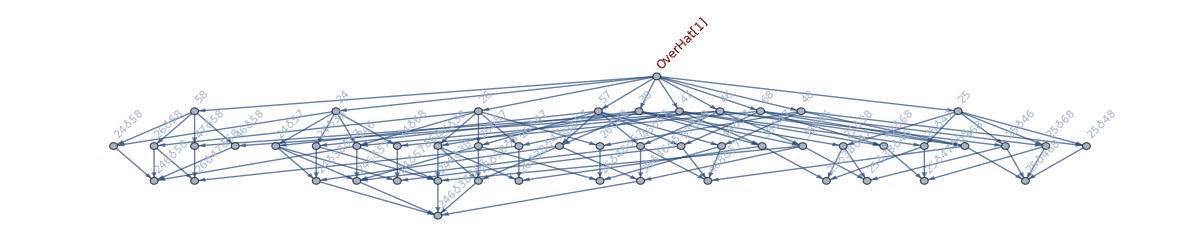
-Graphics-{{4,1},{5,5},{6,8},{7,5},{8,1}}

```mathematica
With[
{g=FormulaGraphReverse3[FindFullFormula[ gr[[1]]]]},
Labeled[Graph[g,ImageSize-> {1200,Automatic},GraphHighlight->HighGr[g]],FormulaLevels[VertexList[HighGr[g]]]]
]
```